## Compare20x20Reps.nb Loads dWvH.m, OS.m, and nmSG.m, demonstrates their holoraumy and calculates their gadgets, etc. as explained in the paper

```mathematica
$Assumptions = Element[n,Reals]
```

n∈ℝ

## Import Adinkra.wl

```mathematica
<<Adinkra.wl
```

```mathematica
BuildDate[Adinkra]
```

181216

### Function Lists

```mathematica
FunctionList[Adinkra]
```

SpaceTime:
IndexRange[SpaceTime][Index], Index = mu, a, or RaiseCode

coordinates, Ϛ[mu], η[mu,nu], Cmetric[[a,b]], InverseCmetric[[a,b]], UD[Field,Ϛ[mu]] , Lap[Field], UP, DOWN, RaiseSTIndex[Field,RaiseCode1,RaiseCode2,...,RaiseCoden], RaiseFermionIndex[Field]

****************************************************************************************
****************************************************************************************

GenerateLandR:
NColors[D,Phi,Psi], LTable[DColor,Phi,Psi], RTable[DColor,Phi,Psi],GenerateLandR[DColor,Phi,Psi,Rep]

****************************************************************************************
****************************************************************************************

AdinkraEssentials:
IndexRange[AdinkraEssentials][Index], Index = p1, II, ReportLevel, or pm

***IMPORTANT****: Default Settings are VScaleFactor = VtildeScaleFactor = -I, VsoNScaleFactor = -I/(2 VsoNScaleFactor), VtildesoNScaleFactor = -I/(2 VtildesoNScaleFactor)

Reports: AdinkraReport[Rep,ReportLevel], AdinkraPreliminaryReport[L,R], AdinkraPreliminaryReport[Rep], AdinkraPreliminaryReportO[Rep], AdinkraHoloMonoReport[Rep], AdinkraSummaryReport[Rep], AdinkraFullReport[Rep]

Basic Functions: nMatrices[Matrices], nRows[Matrices], nColumns[Matrices], Commute[Matrix1,Matrix2], NColors[Rep], NColors[L,R], dmin[N], dbosons[Rep], dbosons[L,R], dfermions[Rep], dfermions[L,R], WordW[{p1,p2,...,pN}]

Intense Calculations: Gadget[Rep1,Rep2], BosonGadget[Rep1,Rep2], ListOfIdenticalMonoOrHolo[MonoOrHolo,Rep], NumDistinctHoloOrMono[HoloOrMono,Rep]

Print Functions: PrintL[Rep][II], PrintR[Rep][II], PrintGALR[Rep][II,JJ], PrintGARL[Rep][II,JJ], PrintV[Rep][II,JJ], PrintVtilde[Rep][II,JJ], PrintZetaGen[Rep][II], PrintHoloraumy[Rep][{p1,p2,...,pN}], PrintMonodromy[Rep][{p1,p2,...,pN}],PrintZetatildeGen[Rep][II], PrintHoloraumytilde[Rep][{p1,p2,...,pN}], PrintMonodromytilde[Rep][{p1,p2,...,pN}], PrintVtildePM[pm][Rep][II,JJ], PrintVtildePM[pm][Rep][II,JJ], PrintAllL[Rep], PrintAllR[Rep], PrintAllGALR[Rep], PrintAllGARL[Rep], PrintAllV[Rep], PrintAllVtilde[Rep], PrintAllZetaGen[Rep], PrintAllHoloraumy[Rep], PrintAllMonodromy[Rep],PrintAllZetatildeGen[Rep], PrintAllHoloraumytilde[Rep], PrintAllMonodromytilde[Rep], PrintAllVtildePM[pm][Rep], PrintAllVtildePM[pm][Rep], ,PrintSigmaProduct[Matrix], PrintLSigmaProduct[Rep], PrintRSigmaProduct[Rep]

Test Functions: CorrectDimensions[Rep], CorrectDimensions[L,R], TransposeTest[Rep], TransposeTest[L,R], InverseTest[Rep], InverseTest[L,R], RO[Rep], Chi0Report[L,R], GATest[Rep], GATest[L,R], soNTest[Matrices], su2Test[MgenPM[pm]][Rep], MutuallyCommuteTest[M1,M2], LinearlyIndependent[Mgen]

Data generated by GenerateAdinkraData[Rep], GenerateAdinkraData[Rep,Orthogonal], GenerateAdinkraDataO[Rep], GenerateAdinkraData[Rep,L], or GenerateAdinkraData[Rep,L,R]:
L[Rep], R[Rep], GALR[Rep], GARL[Rep], chi0[Rep], ncis[Rep], ntrans[Rep], V[Rep], Vtilde[Rep], VsoN[Rep], VtildesoN[Rep], ZetaGen[Rep], Holoraumy[Rep], Monodromy[Rep], ZetatildeGen[Rep], Holoraumytilde[Rep], Monodromytilde[Rep], VPM[pm][Rep], VtildePM[pm][Rep], VsoNPM[pm][Rep], VtildesoNPM[pm][Rep] cSoln[V[Rep]], cSoln[Vtilde[Rep]]

****************************************************************************************
****************************************************************************************

BasisDecomposition:
IndexRange[BasisDecomposition][Index], Index = mu, ahat, a, d, or n

General Matrix Tools:
sigma[mu], αmatrix[ahat], βmatrix[ahat], SigmaProduct[mu1,mu2,...,mun], SigmaProductMF[mu1,mu2,...,mun], SigmaMatrixProduct[mu,AnyMatrix], ρmatrix[mu,nu], ωmatrix[n][a], Basis[d][a,mu,nu], TestOrthogonalσ, TestρOrthogonal, TestωOrthogonal[n], TestBasisOrthogonal[d], Coeffs[d][Matrix][a,mu,nu]

GenerateCoeffs[Rep] generates adinkra representation specific functions:
LCoeffs[Rep][II], CheckLCoeffs[Rep], RCoeffs[Rep][II], CheckRCoeffs[Rep], VCoeffs[Rep][II,JJ], CheckVCoeffs[Rep], VtildeCoeffs[Rep][II,JJ], CheckVtildeCoeffs[Rep], VPMCoeffs[pm][Rep][II,JJ], CheckVPMCoeffs[pm][Rep], VtildePMCoeffs[pm][Rep][II,JJ], CheckVtildePMCoeffs[pm][Rep], NumberNonZero[LCoeffsMat], CoeffsSummaryReport[Rep], CoeffsFullReport[Rep_]

Print Functions:
 PrintSigmaProduct[Matrix], PrintBasis[Matrix], PrintLBasis[Rep][II], PrintRBasis[Rep][II], PrintGALRBasis[Rep][II,JJ], PrintGARLBasis[Rep][II,JJ], PrintVBasis[Rep][II,JJ], PrintVtildeBasis[Rep][II,JJ], PrintVPMBasis[pm][Rep][II,JJ], PrintVtildePMBasis[pm][Rep][II,JJ], PrintLSigmaProduct[Rep], PrintRSigmaProduct[Rep]

****************************************************************************************
****************************************************************************************

BC4Tools:

IndexRange[BC4Tools][Index], Index = n, a, μ, A, II, or tt

Functions: 
HPerm[a], H[[a]], S3Perm[μ], S3[[μ]], VierPerm[A], Vier[[A]], BC4[[n,a,μ,A,II,JJ]] , BC4Perm[n,a,μ,A][[II,JJ]], QuaternionTestIJK[Quat], QuaternionTestKJI[Quat], Digit[Num,Pow], ell[Rep][tt,a][II,JJ], kappa[Rep][ti,a][II,JJ], IellABColor[Rep][[a]], PrintIell[Rep][[a]], IellABCode[Rep][[a]], AntisymmetryCheck[Object1], BC4Color[n,a,μ,A][L], BC4ColorPerm[n,a,μ,A][L],BC4Boson[n,a,μ,A][L],BC4BosonPerm[n,a,μ,A][L], HList,S3List,VierList,PrintBC4Perm[n,a,μ,A],PrintBC4BosonPerm[n,a,μ,A],PrintBC4FermionPerm[n,a,μ,A],PrintBC4ColorPerm[n,a,μ,A],L[Q],L[Qtilde],L[RepCode]

****************************************************************************************
****************************************************************************************

GraphingTools:
IndexRange[GraphingTools][list]

 AdinkraGreen, AdinkraViolet, AdinkraOrange, AdinkraRed, padLmatrix[L], adjacencyToEdge[mat,col], buildrules[list], Valise, GraphAdinkra[L], GraphAdinkra[L,BuildRules[list], ExportAdinkra[L,BuildRules[list],filename]

****************************************************************************************
****************************************************************************************

## Importing Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\kstif\Documents\Data\20x20

```mathematica
Get["dWvH.m"]
```

L, R, GALR, GARL, V, Vtilde, VPM, VtildePM, LCoeffs, RCoeffs, GALRCoeffs, GARLCoeffs, VCoeffs, VtildeCoeffs, VPMCoeffs, VtildePMCoeffs, ncis, ntrans, chi0, and nzvalue for Rep = dWvH are loaded

```mathematica
Get["nmSG.m"]
```

L, R, GALR, GARL, V, Vtilde, VPM, VtildePM, LCoeffs, RCoeffs, GALRCoeffs, GARLCoeffs, VCoeffs, VtildeCoeffs, VPMCoeffs, VtildePMCoeffs, ncis, ntrans, chi0, and nzvalue for Rep = nmSG are loaded

```mathematica
Get["OS.m"]
```

L, R, GALR, GARL, V, Vtilde, VPM, VtildePM, LCoeffs, RCoeffs, GALRCoeffs, GARLCoeffs, VCoeffs, VtildeCoeffs, VPMCoeffs, VtildePMCoeffs, ncis, ntrans, chi0, and nzvalue for Rep = OS are loaded

```mathematica
Get["dWvHprime.m"]
```

L, R, V, Vtilde, VPM, VtildePM, LCoeffs, RCoeffs, VCoeffs, VtildeCoeffs, VPMCoeffs, VtildePMCoeffs, ncis, ntrans, chi0, PrintLBasis, PrintRBasis, PrintVBasis, PrintVtildeBasis, PrintVPMBasis, PrintVtildePMBasis, and nzvalue for Rep = dWvHprime are loaded

```mathematica
Get["nmSGprime.m"]
```

L, R, V, Vtilde, VPM, VtildePM, ZetaGen, ZetatildeGen, LCoeffs, RCoeffs, VCoeffs, VtildeCoeffs, VPMCoeffs, VtildePMCoeffs, ncis, ntrans, chi0, and nzvalue for Rep = nmSGprime are loaded, Holoraumy and Monodromy not generated

```mathematica
Get["OSprime.m"]
```

L, R, V, Vtilde, VPM, VtildePM, LCoeffs, RCoeffs, VCoeffs, VtildeCoeffs, VPMCoeffs, VtildePMCoeffs, ncis, ntrans, chi0, and nzvalue for Rep = OSprime are loaded

## Reports

### Level 0: Preliminary

```mathematica
AdinkraReport[OS]
```

N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = 1, (ncis = 3, ntrans = 2)

```mathematica
AdinkraReport[dWvH]
```

N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = 3, (ncis = 4, ntrans = 1)

```mathematica
AdinkraReport[nmSG]
```

N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = -3, (ncis = 1, ntrans = 4)

```mathematica
AdinkraReport[OSprime]
```

N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = 1, (ncis = 3, ntrans = 2)

```mathematica
AdinkraReport[dWvHprime]
```

N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = 3, (ncis = 4, ntrans = 1)

```mathematica
AdinkraReport[nmSGprime]
```

N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = -3, (ncis = 1, ntrans = 4)

### Level 1: V and Vtilde Linear Independence check: all pass

```mathematica
AdinkraReport[OS,1]
```

N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = 1, (ncis = 3, ntrans = 2)
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True

```mathematica
AdinkraReport[dWvH,1]
```

N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = 3, (ncis = 4, ntrans = 1)
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True

```mathematica
AdinkraReport[nmSG,1]
```

N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = -3, (ncis = 1, ntrans = 4)
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True

```mathematica
AdinkraReport[OSprime,1]
```

N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = 1, (ncis = 3, ntrans = 2)
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True

```mathematica
AdinkraReport[dWvHprime,1]
```

N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = 3, (ncis = 4, ntrans = 1)
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True

```mathematica
AdinkraReport[nmSGprime,1]
```

N = 4
dbosons x dfermions = 20 × 20
GATest = True
InverseTest = True
TransposeTest = False
chi0 = -3, (ncis = 1, ntrans = 4)
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True

## Compare prime to unprimed:

```mathematica
L[dWvH]==L[dWvHprime]/.c0prime-> c0//Simplify
```

True

```mathematica
R[dWvH]==R[dWvHprime]/.c0prime-> c0//Simplify
```

True

```mathematica
V[dWvH]==V[dWvHprime]/.c0prime-> c0//Simplify
```

True

```mathematica
Vtilde[dWvH]==Vtilde[dWvHprime]/.c0prime-> c0//Simplify
```

True

```mathematica
L[OS]==L[OSprime]/.s0prime-> s0//Simplify
```

True

```mathematica
L[nmSG]==L[nmSGprime]/.g0prime-> g0//Simplify
```

True

## V and Vtilde for all reps

### All V and Vtilde for dWvH: all are non-zero

```mathematica
PrintAllV[dWvH]
```

{(0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0
-2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | ⅈ
0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | ⅈ | 0 | 0
0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
-2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | -ⅈ
0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | -ⅈ | 0 | 0
0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0),(0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0
2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
PrintAllVtilde[dWvH]/.c0->0
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0)}

### All V and Vtilde for OS: all are non-zero

```mathematica
PrintAllV[OS]
```

{(0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2
2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | -ⅈ/4 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0
0 | 0 | -2 ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2 ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0),(0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/4
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/4 | 0
0 | 0 | -ⅈ | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0
-2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0),(0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ/2 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/4
0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0
0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | 0 | 0 | ⅈ | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0),(0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ/2 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/4
0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | 0 | 0 | ⅈ | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0),(0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/4
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/4 | 0
0 | 0 | -ⅈ | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0
2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2
0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0),(0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2
-2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | -ⅈ/4 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0
0 | 0 | -2 ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2 ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0)}

```mathematica
PrintAllVtilde[OS]/.s0->0
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | 0 | ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | ⅈ/2 | 0),(0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | -ⅈ/2 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | 0 | -ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | -ⅈ/2 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2
ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0),(0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0)}

### All V and Vtilde for nmSG: all are non-zero

```mathematica
PrintAllV[nmSG]
```

{(0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | ⅈ/3 | 0
0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
-ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | -(2 ⅈ)/3 | 0
0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | ⅈ/3 | 0
ⅈ | 0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | ⅈ (3+1/n) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ (1+3 n))/(2 n) | 0 | 0 | 0 | ⅈ/(3 n) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (3 ⅈ n)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 ⅈ)/3 | 0 | 0 | -(2 ⅈ)/(3 n) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
(2 ⅈ)/3 | 0 | 0 | (2 ⅈ)/3 | 0 | (2 ⅈ)/3 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -(ⅈ (1+3 n))/n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (3 ⅈ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2
-ⅈ/2 | 0 | 0 | ⅈ | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (3 ⅈ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0),(0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | ⅈ/3
ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | ⅈ/3
0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | -(2 ⅈ)/3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ (1+3 n))/(2 n) | 0 | 0 | 0 | -ⅈ/(3 n) | 0 | 0 | 0
ⅈ | 0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | ⅈ (3+1/n) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (3 ⅈ n)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(2 ⅈ)/3 | 0 | 0 | 0 | 0 | -(2 ⅈ)/(3 n) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
(2 ⅈ)/3 | 0 | 0 | (2 ⅈ)/3 | 0 | (2 ⅈ)/3 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -(ⅈ (1+3 n))/n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (3 ⅈ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | 0 | (3 ⅈ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
-ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | -1/2 ⅈ (1+3 n) | 0 | 0 | ⅈ/3 | -(2 ⅈ)/3 | 0 | 0
0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0
0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | -1/2 ⅈ (1+3 n) | 0 | 0 | ⅈ/3 | ⅈ/3 | 0 | 0
0 | 0 | 0 | ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | -1/2 ⅈ (1+3 n) | 0 | 0 | ⅈ/3 | ⅈ/3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | (3 ⅈ n)/2 | 0 | 0 | -ⅈ/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 ⅈ)/3 | 0 | 0 | -(2 ⅈ)/3 | 0 | -(2 ⅈ)/3 | 0 | 0 | -(2 ⅈ (1+3 n))/(3 n) | -(2 ⅈ)/(3 n) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(2 ⅈ)/3 | 0 | 0 | (2 ⅈ)/3 | 0 | (2 ⅈ)/3 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0 | -(ⅈ (1+3 n))/n | -(ⅈ (1+3 n))/n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | -ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (3 ⅈ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | (3 ⅈ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | -1/2 ⅈ (1+3 n) | 0 | 0 | -ⅈ/3 | -(2 ⅈ)/3 | 0 | 0
0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0
0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | -1/2 ⅈ (1+3 n) | 0 | 0 | -ⅈ/3 | ⅈ/3 | 0 | 0
0 | 0 | 0 | ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | -1/2 ⅈ (1+3 n) | 0 | 0 | -ⅈ/3 | ⅈ/3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | (3 ⅈ n)/2 | 0 | 0 | ⅈ/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(2 ⅈ)/3 | 0 | 0 | (2 ⅈ)/3 | 0 | (2 ⅈ)/3 | 0 | 0 | 2/3 ⅈ (3+1/n) | -(2 ⅈ)/(3 n) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(2 ⅈ)/3 | 0 | 0 | (2 ⅈ)/3 | 0 | (2 ⅈ)/3 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | ⅈ (3+1/n) | -(ⅈ (1+3 n))/n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | -ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (3 ⅈ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | (3 ⅈ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0),(0 | ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | -ⅈ/3
-ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | -ⅈ/3
0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | (2 ⅈ)/3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ (1+3 n))/(2 n) | 0 | 0 | 0 | -ⅈ/(3 n) | 0 | 0 | 0
ⅈ | 0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | ⅈ (3+1/n) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(3 ⅈ n)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(2 ⅈ)/3 | 0 | 0 | 0 | 0 | (2 ⅈ)/(3 n) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-(2 ⅈ)/3 | 0 | 0 | -(2 ⅈ)/3 | 0 | -(2 ⅈ)/3 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | ⅈ (3+1/n) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(3 ⅈ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | -(3 ⅈ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | ⅈ/3 | 0
0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
-ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | -(2 ⅈ)/3 | 0
0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | ⅈ/3 | 0
-ⅈ | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0 | -(ⅈ (1+3 n))/n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ (1+3 n))/(2 n) | 0 | 0 | 0 | -ⅈ/(3 n) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (3 ⅈ n)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 ⅈ)/3 | 0 | 0 | -(2 ⅈ)/(3 n) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
(2 ⅈ)/3 | 0 | 0 | (2 ⅈ)/3 | 0 | (2 ⅈ)/3 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -(ⅈ (1+3 n))/n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (3 ⅈ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2
-ⅈ/2 | 0 | 0 | ⅈ | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (3 ⅈ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0)}

```mathematica
PrintAllVtilde[nmSG]/.g0->0
```

{(0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 ⅈ (2+4 n) | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n)
0 | 0 | 1/2 ⅈ (2+4 n) | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 1/2 ⅈ (1+3 n) | 0
0 | 0 | 0 | 2 ⅈ n | 0 | 1/2 ⅈ (2+4 n) | 0 | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n)
0 | 0 | 2 ⅈ n | 0 | -1/2 ⅈ (2+4 n) | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 1/2 ⅈ (1+3 n) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 ⅈ n | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (2+4 n) | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 1/2 ⅈ (1+3 n) | 0
0 | 0 | 0 | 2 ⅈ n | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 1/2 ⅈ (2+4 n) | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ (1+3 n))/(4 n) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ (1+3 n))/(4 n) | 0 | 0
0 | 0 | ⅈ (1+3 n) | 0 | -ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ (1+3 n) | 0 | 0 | 0 | -ⅈ (1+3 n) | 0 | 0 | 3/4 ⅈ (1+3 n) | 0
0 | 0 | 0 | -ⅈ (1+3 n) | 0 | -ⅈ (1+3 n) | 0 | 0 | 0 | 0 | -ⅈ (1+3 n) | 0 | 0 | 0 | ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 3/4 ⅈ (1+3 n)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (4 ⅈ n)/(1+3 n) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (4 ⅈ n)/(1+3 n) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 4 ⅈ n | 0 | 4 ⅈ n | 0 | 0 | 0 | 0 | 4 ⅈ n | 0 | 0 | 0 | -(48 ⅈ n^2)/(4+12 n) | 0 | 0 | 0 | 0 | -ⅈ (1+3 n)
0 | 0 | 4 ⅈ n | 0 | -4 ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅈ n | 0 | 0 | 0 | -(48 ⅈ n^2)/(4+12 n) | 0 | 0 | ⅈ (1+3 n) | 0),(0 | 0 | -1/2 ⅈ (2+4 n) | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | -1/2 ⅈ (1+3 n) | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 ⅈ (2+4 n) | 0 | 0 | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ n | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (2+4 n) | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 ⅈ n | 0 | 1/2 ⅈ (2+4 n) | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | -1/2 ⅈ (1+3 n) | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 ⅈ n | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (2+4 n) | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 1/2 ⅈ (1+3 n) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ n | 0 | 0 | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 1/2 ⅈ (2+4 n) | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ (1+3 n))/(4 n)
0 | 0 | -ⅈ (1+3 n) | 0 | ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ (1+3 n) | 0 | 0 | 0 | ⅈ (1+3 n) | 0 | 0 | -3/4 ⅈ (1+3 n) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ (1+3 n))/(4 n) | 0 | 0
ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | ⅈ (1+3 n) | 0 | 0 | -ⅈ (1+3 n) | 0 | 0 | 0 | -ⅈ (1+3 n) | 0 | 0 | -3/4 ⅈ (1+3 n) | 0 | 0 | 0
0 | 0 | -4 ⅈ n | 0 | 4 ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 4 ⅈ n | 0 | 0 | 0 | (48 ⅈ n^2)/(4+12 n) | 0 | 0 | -ⅈ (1+3 n) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (4 ⅈ n)/(1+3 n) | 0 | 0 | 0 | 0 | 0
-4 ⅈ n | 0 | 0 | 0 | 0 | 0 | -4 ⅈ n | 0 | 0 | 4 ⅈ n | 0 | 0 | 0 | (48 ⅈ n^2)/(4+12 n) | 0 | 0 | ⅈ (1+3 n) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (4 ⅈ n)/(1+3 n) | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ (1+2 n) | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n)
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ (1+2 n) | 0 | 0 | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ n | 0 | 0 | 0 | 0 | 0 | -ⅈ (1+2 n) | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0
0 | 0 | 0 | 2 ⅈ n | 0 | ⅈ (1+2 n) | 0 | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n)
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2 ⅈ n | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | -ⅈ (1+2 n) | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n)
-2 ⅈ n | 0 | 0 | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | ⅈ (1+2 n) | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ (1+3 n) | 0 | ⅈ (1+3 n) | 0 | 0 | 0 | 0 | ⅈ (1+3 n) | 0 | 0 | 0 | -3 ⅈ n | 0 | 0 | 0 | 0 | -(ⅈ (1+3 n)^2)/(4 n)
-ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | -ⅈ (1+3 n) | 0 | 0 | ⅈ (1+3 n) | 0 | 0 | 0 | 3 ⅈ n | 0 | 0 | (ⅈ (1+3 n)^2)/(4 n) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 4 ⅈ n | 0 | 4 ⅈ n | 0 | 0 | 0 | 0 | 4 ⅈ n | 0 | 0 | 0 | -4 ⅈ n | 0 | 0 | 0 | 0 | -3 ⅈ n
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
-4 ⅈ n | 0 | 0 | 0 | 0 | 0 | -4 ⅈ n | 0 | 0 | 4 ⅈ n | 0 | 0 | 0 | 4 ⅈ n | 0 | 0 | 3 ⅈ n | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ (1+2 n) | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 1/2 ⅈ (1+3 n) | 0
0 | -ⅈ (1+2 n) | 0 | 0 | 0 | 0 | 0 | 2 ⅈ n | -2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 0 | -ⅈ (1+2 n) | 2 ⅈ n | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 ⅈ n | 0 | ⅈ (1+2 n) | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | -1/2 ⅈ (1+3 n) | 0
0 | 0 | 2 ⅈ n | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ (1+2 n) | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 1/2 ⅈ (1+3 n) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 0 | -2 ⅈ n | ⅈ (1+2 n) | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0
0 | 0 | ⅈ (1+3 n) | 0 | -ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ (1+3 n) | 0 | 0 | 0 | -3 ⅈ n | 0 | 0 | (ⅈ (1+3 n)^2)/(4 n) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | ⅈ (1+3 n) | -ⅈ (1+3 n) | 0 | 0 | 0 | 3 ⅈ n | 0 | 0 | 0 | 0 | -(ⅈ (1+3 n)^2)/(4 n) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | -4 ⅈ n | 0 | 4 ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 4 ⅈ n | 0 | 0 | 0 | 4 ⅈ n | 0 | 0 | -3 ⅈ n | 0
0 | 4 ⅈ n | 0 | 0 | 0 | 0 | 0 | -4 ⅈ n | 4 ⅈ n | 0 | 0 | 0 | -4 ⅈ n | 0 | 0 | 0 | 0 | 3 ⅈ n | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0),(0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 ⅈ (2+4 n) | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n)
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 ⅈ (2+4 n) | 0 | 0 | 0 | 0 | 0 | -2 ⅈ n | 2 ⅈ n | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (2+4 n) | 2 ⅈ n | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 ⅈ n | 0 | 1/2 ⅈ (2+4 n) | 0 | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n)
0 | 0 | 0 | -2 ⅈ n | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | -1/2 ⅈ (2+4 n) | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 0 | -2 ⅈ n | 1/2 ⅈ (2+4 n) | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ (1+3 n) | 0 | -ⅈ (1+3 n) | 0 | 0 | 0 | 0 | -ⅈ (1+3 n) | 0 | 0 | 0 | ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 3/4 ⅈ (1+3 n)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ (1+3 n))/(4 n) | 0
0 | ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | -ⅈ (1+3 n) | ⅈ (1+3 n) | 0 | 0 | 0 | -ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 3/4 ⅈ (1+3 n) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ (1+3 n))/(4 n) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(4 ⅈ n)/(1+3 n) | 0 | 0 | 0 | 0
0 | 0 | 0 | 4 ⅈ n | 0 | 4 ⅈ n | 0 | 0 | 0 | 0 | 4 ⅈ n | 0 | 0 | 0 | -(48 ⅈ n^2)/(4+12 n) | 0 | 0 | 0 | 0 | -ⅈ (1+3 n)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(4 ⅈ n)/(1+3 n) | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 ⅈ n | 0 | 0 | 0 | 0 | 0 | -4 ⅈ n | 4 ⅈ n | 0 | 0 | 0 | -(48 ⅈ n^2)/(4+12 n) | 0 | 0 | 0 | 0 | ⅈ (1+3 n) | 0 | 0),(0 | -1/2 ⅈ (2+4 n) | 0 | 0 | 0 | 0 | 0 | 2 ⅈ n | -2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0
1/2 ⅈ (2+4 n) | 0 | 0 | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2 ⅈ n | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ (2+4 n) | -2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0
-2 ⅈ n | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (2+4 n) | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0
2 ⅈ n | 0 | 0 | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | -1/2 ⅈ (2+4 n) | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0
0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 0 | -2 ⅈ n | 1/2 ⅈ (2+4 n) | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | ⅈ (1+3 n) | 0 | 0 | -ⅈ (1+3 n) | 0 | 0 | 0 | -ⅈ (1+3 n) | 0 | 0 | -3/4 ⅈ (1+3 n) | 0 | 0 | 0
0 | -ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | ⅈ (1+3 n) | -ⅈ (1+3 n) | 0 | 0 | 0 | ⅈ (1+3 n) | 0 | 0 | 0 | 0 | -3/4 ⅈ (1+3 n) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ (1+3 n))/(4 n) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ (1+3 n))/(4 n)
0 | -4 ⅈ n | 0 | 0 | 0 | 0 | 0 | 4 ⅈ n | -4 ⅈ n | 0 | 0 | 0 | (48 ⅈ n^2)/(4+12 n) | 0 | 0 | 0 | 0 | -ⅈ (1+3 n) | 0 | 0
-4 ⅈ n | 0 | 0 | 0 | 0 | 0 | -4 ⅈ n | 0 | 0 | 4 ⅈ n | 0 | 0 | 0 | (48 ⅈ n^2)/(4+12 n) | 0 | 0 | ⅈ (1+3 n) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(4 ⅈ n)/(1+3 n) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(4 ⅈ n)/(1+3 n) | 0 | 0 | 0 | 0)}

## Vpm and Vtildepm for all Reps

### All Vpm and Vtildepm for dWvH: all are non-zero

```mathematica
LocalRep = dWvH;
```

```mathematica
PrintAllVPM[-1][LocalRep]
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0)}

```mathematica
PrintAllVPM[1][LocalRep]
```

{(0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0
-2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0
0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
PrintAllVtildePM[-1][LocalRep]/.c0->0
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | ⅈ/2 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0)}

```mathematica
PrintAllVtildePM[1][LocalRep]/.c0->0
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0),(0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | -ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2
-ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0),(0 | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | -ⅈ | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | ⅈ | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0)}

```mathematica
Clear[LocalRep]
```

### All Vpm and Vtildepm for OS: all are non-zero

```mathematica
LocalRep = OS;
```

```mathematica
PrintAllVPM[-1][LocalRep]
```

{(0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
PrintAllVPM[1][LocalRep]
```

{(0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/4 | 0
0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/4 | 0
0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0),(0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/4
0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0)}

```mathematica
PrintAllVtildePM[-1][LocalRep]/.s0->0
```

{(0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0
-ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | -ⅈ/4
0 | 0 | ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | -ⅈ/4 | 0
0 | 0 | 0 | ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | ⅈ/4
0 | 0 | ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | -ⅈ/4 | 0
0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0
ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | ⅈ/4 | 0 | 0 | 0
-ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0
0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | ⅈ/4 | 0 | 0
0 | 0 | ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | -ⅈ/4 | 0
0 | 0 | 0 | ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | ⅈ/4
ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | (3 ⅈ)/4 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0
0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | -ⅈ/2 | 0 | 0 | 0 | -(3 ⅈ)/4 | 0 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0
0 | 0 | -ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -(3 ⅈ)/4 | 0 | 0 | -ⅈ/4 | 0
0 | 0 | 0 | ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | (3 ⅈ)/4 | 0 | 0 | 0 | 0 | -ⅈ/4
0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | (3 ⅈ)/4 | 0 | 0
-ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | -(3 ⅈ)/4 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | -(3 ⅈ)/4
0 | 0 | -ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | (3 ⅈ)/4 | 0),(0 | 0 | -ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | ⅈ/4 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | -ⅈ/4
ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | ⅈ/4 | 0 | 0 | 0
0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0
-ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0
0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0
0 | 0 | -ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | ⅈ/4 | 0
0 | 0 | 0 | ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | ⅈ/4
0 | 0 | 0 | -ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | -ⅈ/4
0 | 0 | ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | -ⅈ/4 | 0
0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0
-ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0
0 | 0 | 0 | ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | (3 ⅈ)/4
0 | 0 | ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | -(3 ⅈ)/4 | 0
0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | (3 ⅈ)/4 | 0 | 0
-ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | -(3 ⅈ)/4 | 0 | 0 | 0
0 | 0 | ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | (3 ⅈ)/4 | 0 | 0 | ⅈ/4 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | -(3 ⅈ)/4 | 0 | 0 | 0 | 0 | ⅈ/4
ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | (3 ⅈ)/4 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0
0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | -ⅈ/2 | 0 | 0 | 0 | -(3 ⅈ)/4 | 0 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0),(0 | 0 | 0 | -ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | -ⅈ/4
0 | 0 | ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | -ⅈ/4 | 0
0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | ⅈ/4 | 0 | 0
ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | ⅈ/4 | 0 | 0 | 0
0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0
ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | ⅈ/4 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | -ⅈ/4
0 | 0 | -ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | ⅈ/4 | 0
0 | 0 | ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | -ⅈ/4 | 0
0 | 0 | 0 | ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | ⅈ/4
ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | ⅈ/4 | 0 | 0 | 0
0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0
0 | 0 | -ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -(3 ⅈ)/4 | 0 | 0 | -ⅈ/4 | 0
0 | 0 | 0 | ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | (3 ⅈ)/4 | 0 | 0 | 0 | 0 | -ⅈ/4
-ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -(3 ⅈ)/4 | 0 | 0 | ⅈ/4 | 0 | 0 | 0
0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | ⅈ/2 | 0 | 0 | 0 | (3 ⅈ)/4 | 0 | 0 | 0 | 0 | ⅈ/4 | 0 | 0
0 | 0 | 0 | ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | (3 ⅈ)/4
0 | 0 | ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | -(3 ⅈ)/4 | 0
0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | (3 ⅈ)/4 | 0 | 0
-ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | -(3 ⅈ)/4 | 0 | 0 | 0)}

```mathematica
PrintAllVtildePM[1][LocalRep]/.s0->0
```

{(0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | ⅈ/4 | 0 | 0
ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | ⅈ/4 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | -ⅈ/4
0 | 0 | ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | -ⅈ/4 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | -(3 ⅈ)/4 | 0 | 0 | 0 | 0 | -(3 ⅈ)/4
0 | 0 | -ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -(3 ⅈ)/4 | 0 | 0 | (3 ⅈ)/4 | 0
0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | ⅈ/2 | 0 | 0 | 0 | (3 ⅈ)/4 | 0 | 0 | 0 | 0 | -(3 ⅈ)/4 | 0 | 0
ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | (3 ⅈ)/4 | 0 | 0 | (3 ⅈ)/4 | 0 | 0 | 0
-ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | ⅈ/4 | 0 | 0 | 0
0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0
0 | 0 | -ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | -ⅈ/4 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | ⅈ/4
ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | ⅈ/4 | 0 | 0 | 0
0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | ⅈ/4 | 0 | 0
0 | 0 | ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | -ⅈ/4 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | -ⅈ/4
0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | ⅈ/4 | 0 | 0
-ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0
0 | 0 | 0 | ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | ⅈ/4
0 | 0 | ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | -ⅈ/4 | 0),(0 | 0 | -ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | ⅈ/4 | 0
0 | 0 | 0 | ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | ⅈ/4
ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | ⅈ/4 | 0 | 0 | 0
0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | ⅈ/4 | 0 | 0
ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0
0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | ⅈ/4 | 0 | 0
0 | 0 | ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | ⅈ/4 | 0
0 | 0 | 0 | ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | -ⅈ/4
0 | 0 | 0 | -ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | -(3 ⅈ)/4 | 0 | 0 | 0 | 0 | -(3 ⅈ)/4
0 | 0 | -ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -(3 ⅈ)/4 | 0 | 0 | (3 ⅈ)/4 | 0
0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | ⅈ/2 | 0 | 0 | 0 | (3 ⅈ)/4 | 0 | 0 | 0 | 0 | -(3 ⅈ)/4 | 0 | 0
ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | (3 ⅈ)/4 | 0 | 0 | (3 ⅈ)/4 | 0 | 0 | 0
0 | 0 | 0 | ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | ⅈ/4
0 | 0 | -ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | ⅈ/4 | 0
0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | ⅈ/4 | 0 | 0
ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | ⅈ/4 | 0 | 0 | 0
0 | 0 | -ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | ⅈ/4 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | -ⅈ/4
-ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0
0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | ⅈ/4 | 0 | 0),(0 | 0 | 0 | -ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | -(3 ⅈ)/4 | 0 | 0 | 0 | 0 | -(3 ⅈ)/4
0 | 0 | -ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -(3 ⅈ)/4 | 0 | 0 | (3 ⅈ)/4 | 0
0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | ⅈ/2 | 0 | 0 | 0 | (3 ⅈ)/4 | 0 | 0 | 0 | 0 | -(3 ⅈ)/4 | 0 | 0
ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | (3 ⅈ)/4 | 0 | 0 | (3 ⅈ)/4 | 0 | 0 | 0
0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0
-ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0
0 | 0 | 0 | ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | ⅈ/4
0 | 0 | -ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | ⅈ/4 | 0
0 | 0 | ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | -ⅈ/4 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | -ⅈ/4
-ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0
0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0
0 | 0 | -ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | -ⅈ/4 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | ⅈ/4
ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0
0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | -ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | ⅈ/4 | 0 | 0
0 | 0 | 0 | -ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | ⅈ/4
0 | 0 | ⅈ/2 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | ⅈ/4 | 0
0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | ⅈ/2 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0
ⅈ/2 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0)}

```mathematica
Clear[LocalRep]
```

### All Vpm and Vtildepm for nmSG: all are non-zero

```mathematica
LocalRep = nmSG;
```

```mathematica
PrintAllVPM[-1][LocalRep]
```

{(0 | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | ⅈ (3+1/n) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ (1+3 n))/(2 n) | 0 | 0 | 0 | ⅈ/(3 n) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 ⅈ)/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ (1+3 n))/(2 n) | 0 | 0 | 0 | -ⅈ/(3 n) | 0 | 0 | 0
ⅈ | 0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | ⅈ (3+1/n) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(2 ⅈ)/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | -ⅈ/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | -ⅈ/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | -ⅈ/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | ⅈ/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(2 ⅈ)/3 | 0 | 0 | (2 ⅈ)/3 | 0 | (2 ⅈ)/3 | 0 | 0 | 2/3 ⅈ (3+1/n) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | ⅈ (3+1/n) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
PrintAllVPM[1][LocalRep]
```

{(0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | ⅈ/3 | 0
0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
-ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | -(2 ⅈ)/3 | 0
0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | ⅈ/3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (3 ⅈ n)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 ⅈ)/(3 n) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
(2 ⅈ)/3 | 0 | 0 | (2 ⅈ)/3 | 0 | (2 ⅈ)/3 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ (1+3 n))/n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (3 ⅈ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2
-ⅈ/2 | 0 | 0 | ⅈ | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (3 ⅈ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0),(0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | ⅈ/3
ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | ⅈ/3
0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | -(2 ⅈ)/3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (3 ⅈ n)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 ⅈ)/(3 n) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
(2 ⅈ)/3 | 0 | 0 | (2 ⅈ)/3 | 0 | (2 ⅈ)/3 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ (1+3 n))/n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (3 ⅈ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | 0 | (3 ⅈ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
-ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | -(2 ⅈ)/3 | 0 | 0
0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0
0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | ⅈ/3 | 0 | 0
0 | 0 | 0 | ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | ⅈ/3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (3 ⅈ n)/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | ⅈ/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 ⅈ)/(3 n) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(2 ⅈ)/3 | 0 | 0 | (2 ⅈ)/3 | 0 | (2 ⅈ)/3 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ (1+3 n))/n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | -ⅈ/2 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (3 ⅈ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2
0 | 0 | (3 ⅈ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0)}

```mathematica
PrintAllVtildePM[-1][LocalRep]/.g0->0
```

{(0 | ⅈ (1+n) | 0 | 0 | 0 | 0 | 0 | -ⅈ n | ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 1/4 ⅈ (1+3 n) | 0 | 0
-ⅈ (1+n) | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0 | 0 | 0
0 | 0 | 0 | -ⅈ (1+n) | 0 | -ⅈ n | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 1/4 ⅈ (1+3 n)
0 | 0 | ⅈ (1+n) | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0
0 | 0 | 0 | ⅈ n | 0 | ⅈ (1+n) | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | -1/4 ⅈ (1+3 n)
0 | 0 | ⅈ n | 0 | -ⅈ (1+n) | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0
0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | -ⅈ (1+n) | ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 1/4 ⅈ (1+3 n) | 0 | 0
ⅈ n | 0 | 0 | 0 | 0 | 0 | ⅈ (1+n) | 0 | 0 | -ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | -1/4 ⅈ (1+3 n) | 0 | 0 | 0
-ⅈ n | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | ⅈ (1+n) | 0 | 0 | 0 | ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0 | 0 | 0
0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | ⅈ n | -ⅈ (1+n) | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | -1/4 ⅈ (1+3 n) | 0 | 0
0 | 0 | ⅈ n | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ (1+n) | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0
0 | 0 | 0 | ⅈ n | 0 | ⅈ n | 0 | 0 | 0 | 0 | ⅈ (1+n) | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | -1/4 ⅈ (1+3 n)
-1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | (ⅈ (-1+9 n^2))/(8 n) | 0 | 0 | 0
0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | (ⅈ (-1+9 n^2))/(8 n) | 0 | 0
0 | 0 | 1/2 ⅈ (1+3 n) | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | (ⅈ (-1+9 n^2))/(8 n) | 0
0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | (ⅈ (-1+9 n^2))/(8 n)
0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 0 | -2 ⅈ n | 2 ⅈ n | 0 | 0 | 0 | 1/2 ((4 ⅈ n)/(1+3 n)-(48 ⅈ n^2)/(4+12 n)) | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0
2 ⅈ n | 0 | 0 | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | 1/2 ((4 ⅈ n)/(1+3 n)-(48 ⅈ n^2)/(4+12 n)) | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0
0 | 0 | 0 | 2 ⅈ n | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 1/2 ((4 ⅈ n)/(1+3 n)-(48 ⅈ n^2)/(4+12 n)) | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n)
0 | 0 | 2 ⅈ n | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | 1/2 ((4 ⅈ n)/(1+3 n)-(48 ⅈ n^2)/(4+12 n)) | 0 | 0 | 1/2 ⅈ (1+3 n) | 0),(0 | 0 | -ⅈ (1+n) | 0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | -1/4 ⅈ (1+3 n) | 0
0 | 0 | 0 | -ⅈ (1+n) | 0 | -ⅈ n | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 1/4 ⅈ (1+3 n)
ⅈ (1+n) | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | -ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | -1/4 ⅈ (1+3 n) | 0 | 0 | 0
0 | ⅈ (1+n) | 0 | 0 | 0 | 0 | 0 | -ⅈ n | ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 1/4 ⅈ (1+3 n) | 0 | 0
-ⅈ n | 0 | 0 | 0 | 0 | 0 | -ⅈ (1+n) | 0 | 0 | ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0 | 0 | 0
0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | -ⅈ (1+n) | ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 1/4 ⅈ (1+3 n) | 0 | 0
0 | 0 | -ⅈ n | 0 | ⅈ (1+n) | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | -1/4 ⅈ (1+3 n) | 0
0 | 0 | 0 | ⅈ n | 0 | ⅈ (1+n) | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | -1/4 ⅈ (1+3 n)
0 | 0 | 0 | -ⅈ n | 0 | -ⅈ n | 0 | 0 | 0 | 0 | -ⅈ (1+n) | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 1/4 ⅈ (1+3 n)
0 | 0 | ⅈ n | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ (1+n) | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0
0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | -ⅈ n | ⅈ (1+n) | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 1/4 ⅈ (1+3 n) | 0 | 0
-ⅈ n | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | ⅈ (1+n) | 0 | 0 | 0 | ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0 | 0 | 0
0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | (ⅈ (-1+9 n^2))/(8 n)
0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | -(ⅈ (-1+9 n^2))/(8 n) | 0
0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | (ⅈ (-1+9 n^2))/(8 n) | 0 | 0
1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | -(ⅈ (-1+9 n^2))/(8 n) | 0 | 0 | 0
0 | 0 | -2 ⅈ n | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 1/2 (-(4 ⅈ n)/(1+3 n)+(48 ⅈ n^2)/(4+12 n)) | 0 | 0 | -1/2 ⅈ (1+3 n) | 0
0 | 0 | 0 | 2 ⅈ n | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 1/2 ((4 ⅈ n)/(1+3 n)-(48 ⅈ n^2)/(4+12 n)) | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n)
-2 ⅈ n | 0 | 0 | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 1/2 (-(4 ⅈ n)/(1+3 n)+(48 ⅈ n^2)/(4+12 n)) | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0
0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 0 | -2 ⅈ n | 2 ⅈ n | 0 | 0 | 0 | 1/2 ((4 ⅈ n)/(1+3 n)-(48 ⅈ n^2)/(4+12 n)) | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0),(0 | 0 | 0 | -ⅈ (1+n) | 0 | -ⅈ n | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 1/4 ⅈ (1+3 n)
0 | 0 | ⅈ (1+n) | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0
0 | -ⅈ (1+n) | 0 | 0 | 0 | 0 | 0 | ⅈ n | -ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | -1/4 ⅈ (1+3 n) | 0 | 0
ⅈ (1+n) | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | -ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | -1/4 ⅈ (1+3 n) | 0 | 0 | 0
0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | -ⅈ (1+n) | ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 1/4 ⅈ (1+3 n) | 0 | 0
ⅈ n | 0 | 0 | 0 | 0 | 0 | ⅈ (1+n) | 0 | 0 | -ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | -1/4 ⅈ (1+3 n) | 0 | 0 | 0
0 | 0 | 0 | -ⅈ n | 0 | -ⅈ (1+n) | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 1/4 ⅈ (1+3 n)
0 | 0 | -ⅈ n | 0 | ⅈ (1+n) | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | -1/4 ⅈ (1+3 n) | 0
0 | 0 | ⅈ n | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ (1+n) | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0
0 | 0 | 0 | ⅈ n | 0 | ⅈ n | 0 | 0 | 0 | 0 | ⅈ (1+n) | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | -1/4 ⅈ (1+3 n)
ⅈ n | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | -ⅈ (1+n) | 0 | 0 | 0 | -ⅈ n | 0 | 0 | -1/4 ⅈ (1+3 n) | 0 | 0 | 0
0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | -ⅈ n | ⅈ (1+n) | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 1/4 ⅈ (1+3 n) | 0 | 0
0 | 0 | 1/2 ⅈ (1+3 n) | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 1/2 (ⅈ-3 ⅈ n) | 0 | 0 | (ⅈ (1+3 n)^2)/(8 n) | 0
0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 1/2 (-ⅈ+3 ⅈ n) | 0 | 0 | 0 | 0 | (ⅈ (1+3 n)^2)/(8 n)
1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 1/2 (ⅈ-3 ⅈ n) | 0 | 0 | -(ⅈ (1+3 n)^2)/(8 n) | 0 | 0 | 0
0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 1/2 (-ⅈ+3 ⅈ n) | 0 | 0 | 0 | 0 | -(ⅈ (1+3 n)^2)/(8 n) | 0 | 0
0 | 0 | 0 | -2 ⅈ n | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 1/2 (-ⅈ+3 ⅈ n)
0 | 0 | -2 ⅈ n | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 1/2 (ⅈ-3 ⅈ n) | 0
0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 0 | -2 ⅈ n | 2 ⅈ n | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | 1/2 (-ⅈ+3 ⅈ n) | 0 | 0
2 ⅈ n | 0 | 0 | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 1/2 (ⅈ-3 ⅈ n) | 0 | 0 | 0)}

```mathematica
PrintAllVtildePM[1][LocalRep]/.g0->0
```

{(0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | ⅈ n | -ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | -1/4 ⅈ (1+3 n) | 0 | 0
ⅈ n | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | -ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | -1/4 ⅈ (1+3 n) | 0 | 0 | 0
0 | 0 | 0 | -ⅈ n | 0 | -ⅈ n | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 1/4 ⅈ (1+3 n)
0 | 0 | ⅈ n | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0
0 | 0 | 0 | ⅈ n | 0 | ⅈ n | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | -1/4 ⅈ (1+3 n)
0 | 0 | ⅈ n | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0
0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | ⅈ n | -ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | -1/4 ⅈ (1+3 n) | 0 | 0
-ⅈ n | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0 | 0 | 0
ⅈ n | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | -ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | -1/4 ⅈ (1+3 n) | 0 | 0 | 0
0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | -ⅈ n | ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 1/4 ⅈ (1+3 n) | 0 | 0
0 | 0 | ⅈ n | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0
0 | 0 | 0 | ⅈ n | 0 | ⅈ n | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | -1/4 ⅈ (1+3 n)
1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | -(ⅈ (1+3 n)^2)/(8 n) | 0 | 0 | 0
0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | -(ⅈ (1+3 n)^2)/(8 n) | 0 | 0
0 | 0 | 1/2 ⅈ (1+3 n) | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | (ⅈ (1+3 n)^2)/(8 n) | 0
0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | (ⅈ (1+3 n)^2)/(8 n)
0 | -2 ⅈ n | 0 | 0 | 0 | 0 | 0 | 2 ⅈ n | -2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0
-2 ⅈ n | 0 | 0 | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0
0 | 0 | 0 | 2 ⅈ n | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n)
0 | 0 | 2 ⅈ n | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 1/2 ⅈ (1+3 n) | 0),(0 | 0 | -ⅈ n | 0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | -1/4 ⅈ (1+3 n) | 0
0 | 0 | 0 | ⅈ n | 0 | ⅈ n | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | -1/4 ⅈ (1+3 n)
ⅈ n | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | -ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | -1/4 ⅈ (1+3 n) | 0 | 0 | 0
0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | ⅈ n | -ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | -1/4 ⅈ (1+3 n) | 0 | 0
-ⅈ n | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0 | 0 | 0
0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | ⅈ n | -ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | -1/4 ⅈ (1+3 n) | 0 | 0
0 | 0 | -ⅈ n | 0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | -1/4 ⅈ (1+3 n) | 0
0 | 0 | 0 | -ⅈ n | 0 | -ⅈ n | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 1/4 ⅈ (1+3 n)
0 | 0 | 0 | ⅈ n | 0 | ⅈ n | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | -1/4 ⅈ (1+3 n)
0 | 0 | ⅈ n | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0
0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | ⅈ n | -ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | -1/4 ⅈ (1+3 n) | 0 | 0
-ⅈ n | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0 | 0 | 0
0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | -(ⅈ (1+3 n)^2)/(8 n)
0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | -(ⅈ (1+3 n)^2)/(8 n) | 0
0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | -(ⅈ (1+3 n)^2)/(8 n) | 0 | 0
1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | -(ⅈ (1+3 n)^2)/(8 n) | 0 | 0 | 0
0 | 0 | -2 ⅈ n | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | -1/2 ⅈ (1+3 n) | 0
0 | 0 | 0 | -2 ⅈ n | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n)
-2 ⅈ n | 0 | 0 | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0
0 | -2 ⅈ n | 0 | 0 | 0 | 0 | 0 | 2 ⅈ n | -2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0),(0 | 0 | 0 | ⅈ n | 0 | ⅈ n | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | -1/4 ⅈ (1+3 n)
0 | 0 | ⅈ n | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0
0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | ⅈ n | -ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | -1/4 ⅈ (1+3 n) | 0 | 0
-ⅈ n | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0 | 0 | 0
0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | -ⅈ n | ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 1/4 ⅈ (1+3 n) | 0 | 0
-ⅈ n | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0 | 0 | 0
0 | 0 | 0 | ⅈ n | 0 | ⅈ n | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | -1/4 ⅈ (1+3 n)
0 | 0 | -ⅈ n | 0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | -1/4 ⅈ (1+3 n) | 0
0 | 0 | ⅈ n | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0
0 | 0 | 0 | -ⅈ n | 0 | -ⅈ n | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 0 | 0 | 1/4 ⅈ (1+3 n)
-ⅈ n | 0 | 0 | 0 | 0 | 0 | -ⅈ n | 0 | 0 | ⅈ n | 0 | 0 | 0 | ⅈ n | 0 | 0 | 1/4 ⅈ (1+3 n) | 0 | 0 | 0
0 | ⅈ n | 0 | 0 | 0 | 0 | 0 | -ⅈ n | ⅈ n | 0 | 0 | 0 | -ⅈ n | 0 | 0 | 0 | 0 | 1/4 ⅈ (1+3 n) | 0 | 0
0 | 0 | 1/2 ⅈ (1+3 n) | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | -1/8 ⅈ (4+12 n) | 0 | 0 | (ⅈ (1+3 n)^2)/(8 n) | 0
0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | -1/8 ⅈ (4+12 n) | 0 | 0 | 0 | 0 | -(ⅈ (1+3 n)^2)/(8 n)
-1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 1/2 (ⅈ+3 ⅈ n) | 0 | 0 | (ⅈ (1+3 n)^2)/(8 n) | 0 | 0 | 0
0 | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 0 | 0 | 1/2 ⅈ (1+3 n) | -1/2 ⅈ (1+3 n) | 0 | 0 | 0 | 1/2 (ⅈ+3 ⅈ n) | 0 | 0 | 0 | 0 | -(ⅈ (1+3 n)^2)/(8 n) | 0 | 0
0 | 0 | 0 | 2 ⅈ n | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | -1/8 ⅈ (4+12 n)
0 | 0 | -2 ⅈ n | 0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | -1/8 ⅈ (4+12 n) | 0
0 | 2 ⅈ n | 0 | 0 | 0 | 0 | 0 | -2 ⅈ n | 2 ⅈ n | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 0 | 0 | 1/2 (ⅈ+3 ⅈ n) | 0 | 0
-2 ⅈ n | 0 | 0 | 0 | 0 | 0 | -2 ⅈ n | 0 | 0 | 2 ⅈ n | 0 | 0 | 0 | 2 ⅈ n | 0 | 0 | 1/2 (ⅈ+3 ⅈ n) | 0 | 0 | 0)}

```mathematica
Clear[LocalRep]
```

## Eigenvalues: all plus or minus 1 for all reps. nmSG takes a little time to calculate

```mathematica
LocalRep =OS;
```

```mathematica
(Table[Abs[Eigenvalues[V[LocalRep][[II,JJ]]]]==Abs[{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1}] && Element[Eigenvalues[V[LocalRep][[II,JJ]]],Reals],{II,1,3},{JJ,II+1,4}]//Flatten)==Table[True,{Index,1,6}]
```

True

```mathematica
(Table[Abs[Eigenvalues[Vtilde[LocalRep][[II,JJ]]]]==Abs[{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1}]&& Element[Eigenvalues[Vtilde[LocalRep][[II,JJ]]],Reals],{II,1,3},{JJ,II+1,4}]//Flatten)==Table[True,{Index,1,6}]
```

True

```mathematica
Clear[LocalRep]
```

## Print Things in a Tensor Product basis

```mathematica
Table[ωmatrix[5][slIndex]//MatrixForm,{slIndex,0,24}]
```

{(1/(5 nz[5]) | 0 | 0 | 0 | 0
0 | 1/(5 nz[5]) | 0 | 0 | 0
0 | 0 | 1/(5 nz[5]) | 0 | 0
0 | 0 | 0 | 1/(5 nz[5]) | 0
0 | 0 | 0 | 0 | 1/(5 nz[5])),(0 | 1/(2 nz[5]) | 0 | 0 | 0
1/(2 nz[5]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(0 | -1/(2 nz[5]) | 0 | 0 | 0
1/(2 nz[5]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(1/(2 nz[5]) | 0 | 0 | 0 | 0
0 | -1/(2 nz[5]) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(0 | 0 | 1/(2 nz[5]) | 0 | 0
0 | 0 | 0 | 0 | 0
1/(2 nz[5]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(0 | 0 | -1/(2 nz[5]) | 0 | 0
0 | 0 | 0 | 0 | 0
1/(2 nz[5]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0
0 | 0 | 1/(2 nz[5]) | 0 | 0
0 | 1/(2 nz[5]) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0
0 | 0 | -1/(2 nz[5]) | 0 | 0
0 | 1/(2 nz[5]) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(1/(6 nz[5]) | 0 | 0 | 0 | 0
0 | 1/(6 nz[5]) | 0 | 0 | 0
0 | 0 | -1/(3 nz[5]) | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 1/(2 nz[5]) | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1/(2 nz[5]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | -1/(2 nz[5]) | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1/(2 nz[5]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/(2 nz[5]) | 0
0 | 0 | 0 | 0 | 0
0 | 1/(2 nz[5]) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/(2 nz[5]) | 0
0 | 0 | 0 | 0 | 0
0 | 1/(2 nz[5]) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/(2 nz[5]) | 0
0 | 0 | 1/(2 nz[5]) | 0 | 0
0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/(2 nz[5]) | 0
0 | 0 | 1/(2 nz[5]) | 0 | 0
0 | 0 | 0 | 0 | 0),(1/(12 nz[5]) | 0 | 0 | 0 | 0
0 | 1/(12 nz[5]) | 0 | 0 | 0
0 | 0 | 1/(12 nz[5]) | 0 | 0
0 | 0 | 0 | -1/(4 nz[5]) | 0
0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 1/(2 nz[5])
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1/(2 nz[5]) | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | -1/(2 nz[5])
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1/(2 nz[5]) | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(2 nz[5])
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 1/(2 nz[5]) | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/(2 nz[5])
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 1/(2 nz[5]) | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(2 nz[5])
0 | 0 | 0 | 0 | 0
0 | 0 | 1/(2 nz[5]) | 0 | 0),(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/(2 nz[5])
0 | 0 | 0 | 0 | 0
0 | 0 | 1/(2 nz[5]) | 0 | 0),(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(2 nz[5])
0 | 0 | 0 | 1/(2 nz[5]) | 0),(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/(2 nz[5])
0 | 0 | 0 | 1/(2 nz[5]) | 0),(1/(20 nz[5]) | 0 | 0 | 0 | 0
0 | 1/(20 nz[5]) | 0 | 0 | 0
0 | 0 | 1/(20 nz[5]) | 0 | 0
0 | 0 | 0 | 1/(20 nz[5]) | 0
0 | 0 | 0 | 0 | -1/(5 nz[5]))}

### (Ṽ)_IJ for dWVH for c0=0 and nz[5] = 2 as shown in the paper

```mathematica
PrintVtildeBasis[dWvH][1,2]/.c0->0/.nz[5]->2
```

-2 ω_0^5⊗β_3+2 ω_1^5⊗α_1+2 ω_2^5⊗α_1-2 ω_3^5⊗α_2-4 ⅈ ω_5^5⊗I_4+2 ω_6^5⊗α_3-2 ω_7^5⊗α_3+2 ω_8^5⊗α_2+2 ⅈ ω_9^5⊗(α_3 β_2)+2 ⅈ ω_10^5⊗(α_3 β_2)+2 ω_11^5⊗β_2-2 ω_12^5⊗β_2-2 ⅈ ω_13^5⊗(α_1 β_2)-2 ⅈ ω_14^5⊗(α_1 β_2)+5 ω_15^5⊗α_2+3 ω_15^5⊗β_3+2 ⅈ ω_16^5⊗(α_3 β_1)+2 ⅈ ω_17^5⊗(α_3 β_1)+2 ω_18^5⊗β_1-2 ω_19^5⊗β_1-2 ⅈ ω_20^5⊗(α_1 β_1)-2 ⅈ ω_21^5⊗(α_1 β_1)+2 ⅈ ω_23^5⊗I_4-2 ⅈ ω_23^5⊗(α_2 β_3)+5 ω_24^5⊗α_2+3 ω_24^5⊗β_3

```mathematica
PrintVtildeBasis[dWvH][1,3]/.c0->0/.nz[5]->2
```

4 ⅈ ω_2^5⊗I_4+2 ω_4^5⊗α_1+2 ω_5^5⊗α_1+2 ω_6^5⊗α_2+2 ω_7^5⊗α_2-4 ω_8^5⊗α_3-2 ⅈ ω_9^5⊗(α_2 β_2)-2 ⅈ ω_10^5⊗(α_2 β_2)+2 ⅈ ω_11^5⊗(α_1 β_2)+2 ⅈ ω_12^5⊗(α_1 β_2)+2 ω_13^5⊗β_2-2 ω_14^5⊗β_2+5 ω_15^5⊗α_3-3 ω_15^5⊗β_2-2 ⅈ ω_16^5⊗(α_2 β_1)-2 ⅈ ω_17^5⊗(α_2 β_1)+2 ⅈ ω_18^5⊗(α_1 β_1)+2 ⅈ ω_19^5⊗(α_1 β_1)+2 ω_20^5⊗β_1-2 ω_21^5⊗β_1-2 ω_22^5⊗β_1-2 ⅈ ω_23^5⊗(α_3 β_3)+5 ω_24^5⊗α_3+5 ω_24^5⊗β_2

```mathematica
PrintVtildeBasis[dWvH][1,4]/.c0->0/.nz[5]->2
```

2 ω_1^5⊗α_2-2 ω_2^5⊗α_2+2 ω_3^5⊗α_1+2 ω_4^5⊗α_3-2 ω_5^5⊗α_3+4 ⅈ ω_7^5⊗I_4+2 ω_8^5⊗α_1+2 ω_9^5⊗β_2-2 ω_10^5⊗β_2-2 ⅈ ω_11^5⊗(α_3 β_2)-2 ⅈ ω_12^5⊗(α_3 β_2)+2 ⅈ ω_13^5⊗(α_2 β_2)+2 ⅈ ω_14^5⊗(α_2 β_2)+5 ω_15^5⊗α_1+3 ω_15^5⊗β_1+2 ω_16^5⊗β_1-2 ω_17^5⊗β_1-2 ⅈ ω_18^5⊗(α_3 β_1)-2 ⅈ ω_19^5⊗(α_3 β_1)+2 ⅈ ω_20^5⊗(α_2 β_1)+2 ⅈ ω_21^5⊗(α_2 β_1)-2 ω_22^5⊗β_2-2 ⅈ ω_23^5⊗(α_1 β_3)+5 ω_24^5⊗α_1-5 ω_24^5⊗β_1

```mathematica
PrintVtildeBasis[dWvH][2,3]/.c0->0/.nz[5]->2
```

2 ω_1^5⊗α_2-2 ω_2^5⊗α_2+2 ω_3^5⊗α_1+2 ω_4^5⊗α_3-2 ω_5^5⊗α_3+4 ⅈ ω_7^5⊗I_4+2 ω_8^5⊗α_1+2 ω_9^5⊗β_2-2 ω_10^5⊗β_2-2 ⅈ ω_11^5⊗(α_3 β_2)-2 ⅈ ω_12^5⊗(α_3 β_2)+2 ⅈ ω_13^5⊗(α_2 β_2)+2 ⅈ ω_14^5⊗(α_2 β_2)+5 ω_15^5⊗α_1-3 ω_15^5⊗β_1+2 ω_16^5⊗β_1-2 ω_17^5⊗β_1-2 ⅈ ω_18^5⊗(α_3 β_1)-2 ⅈ ω_19^5⊗(α_3 β_1)+2 ⅈ ω_20^5⊗(α_2 β_1)+2 ⅈ ω_21^5⊗(α_2 β_1)+2 ω_22^5⊗β_2-2 ⅈ ω_23^5⊗(α_1 β_3)+5 ω_24^5⊗α_1+5 ω_24^5⊗β_1

```mathematica
PrintVtildeBasis[dWvH][2,4]/.c0->0/.nz[5]->2
```

-4 ⅈ ω_2^5⊗I_4-2 ω_4^5⊗α_1-2 ω_5^5⊗α_1-2 ω_6^5⊗α_2-2 ω_7^5⊗α_2+4 ω_8^5⊗α_3+2 ⅈ ω_9^5⊗(α_2 β_2)+2 ⅈ ω_10^5⊗(α_2 β_2)-2 ⅈ ω_11^5⊗(α_1 β_2)-2 ⅈ ω_12^5⊗(α_1 β_2)-2 ω_13^5⊗β_2+2 ω_14^5⊗β_2-5 ω_15^5⊗α_3-3 ω_15^5⊗β_2+2 ⅈ ω_16^5⊗(α_2 β_1)+2 ⅈ ω_17^5⊗(α_2 β_1)-2 ⅈ ω_18^5⊗(α_1 β_1)-2 ⅈ ω_19^5⊗(α_1 β_1)-2 ω_20^5⊗β_1+2 ω_21^5⊗β_1-2 ω_22^5⊗β_1+2 ⅈ ω_23^5⊗(α_3 β_3)-5 ω_24^5⊗α_3+5 ω_24^5⊗β_2

```mathematica
PrintVtildeBasis[dWvH][2,4]/.c0->0/.nz[5]->2
```

-4 ⅈ ω_2^5⊗I_4-2 ω_4^5⊗α_1-2 ω_5^5⊗α_1-2 ω_6^5⊗α_2-2 ω_7^5⊗α_2+4 ω_8^5⊗α_3+2 ⅈ ω_9^5⊗(α_2 β_2)+2 ⅈ ω_10^5⊗(α_2 β_2)-2 ⅈ ω_11^5⊗(α_1 β_2)-2 ⅈ ω_12^5⊗(α_1 β_2)-2 ω_13^5⊗β_2+2 ω_14^5⊗β_2-5 ω_15^5⊗α_3-3 ω_15^5⊗β_2+2 ⅈ ω_16^5⊗(α_2 β_1)+2 ⅈ ω_17^5⊗(α_2 β_1)-2 ⅈ ω_18^5⊗(α_1 β_1)-2 ⅈ ω_19^5⊗(α_1 β_1)-2 ω_20^5⊗β_1+2 ω_21^5⊗β_1-2 ω_22^5⊗β_1+2 ⅈ ω_23^5⊗(α_3 β_3)-5 ω_24^5⊗α_3+5 ω_24^5⊗β_2

## Gadgets

### Check normalization, all equal 5

```mathematica
Gadget[nmSG,nmSG]==Gadget[OS,OS] ==Gadget[dWvH,dWvH] ==5
```

True

```mathematica
Gadget[dWvH,OS]//Simplify
```

4+3 c0^4+c0^3 (3-12 s0)+s0^2-3 s0^3+3 s0^4+c0 s0 (-2+9 s0-12 s0^2)+c0^2 (1-9 s0+18 s0^2)

```mathematica
Gadget[dWvH,nmSG] //Simplify
```

-1/(12 n)(1+26 n+181 n^2+9 c0^4 (1+3 n)^2+9 g0^4 (1+3 n)^2+18 g0^3 (1+10 n+21 n^2)+6 g0 (1+22 n+97 n^2)+6 g0^2 (3+40 n+117 n^2)+18 c0^3 (1+3 n) (1+7 n+g0 (2+6 n))+6 c0^2 (3+40 n+117 n^2+9 (g0+3 g0 n)^2+9 g0 (1+10 n+21 n^2))+6 c0 (1+22 n+97 n^2+6 g0^3 (1+3 n)^2+9 g0^2 (1+10 n+21 n^2)+g0 (6+80 n+234 n^2)))

```mathematica
Gadget[OS,nmSG]//Simplify
```

-1/(48 n (1+3 n))(27 g0^4 (1+n) (1+3 n)^2+3 (1+2 s0+3 s0^2)^2-3 n^3 (359+1092 s0+918 s0^2+108 s0^3-81 s0^4)+3 n^2 (-177-724 s0-618 s0^2+36 s0^3+135 s0^4)+n (-59-324 s0-222 s0^2+180 s0^3+189 s0^4)+36 g0^3 (1+3 n)^2 (1+3 s0+n (-1+3 s0))+6 g0^2 (1+3 n) (5+18 s0+27 s0^2+9 n^2 (-17-6 s0+9 s0^2)+4 n (-13+9 s0+27 s0^2))+12 g0 (1+3 n) (1+5 s0+9 s0^2+9 s0^3+2 n (-15-26 s0+9 s0^2+18 s0^3)+n^2 (-91-153 s0-27 s0^2+27 s0^3)))

#### Concise forms of Gadget[dWvH, OS], Gadget[dWvH,nmSG], and Gadget[OS,nmSG]

```mathematica
GadgetdWvHOSHazelFactorization = ((s0 - 1 - c0)(1-c0-3 c0^3+(1+9 c0^2) s0-9 c0 s0^2+3 s0^3)+5);
```

```mathematica
Gadget[dWvH,OS]== GadgetdWvHOSHazelFactorization//Simplify
```

True

```mathematica
GadgetdWvHnmSGHazelFactorization = -1/(4n)(3 (3n+1)^2(c0 + g0)^4 + 6 (3n +1)(7n+1)(c0+g0)^3+2(9n+1)(13n+3)(c0+g0)^2+2 (97 n^2+22n + 1)(c0+g0)) - 1/(12 n)(181 n^2+26n+1)
```

-(1+26 n+181 n^2)/(12 n)-(3 (c0+g0)^4 (1+3 n)^2+6 (c0+g0)^3 (1+3 n) (1+7 n)+2 (c0+g0)^2 (1+9 n) (3+13 n)+2 (c0+g0) (1+22 n+97 n^2))/(4 n)

```mathematica
Gadget[dWvH,nmSG]==GadgetdWvHnmSGHazelFactorization//Simplify
```

True

```mathematica
GadgetOSnmSGHazelFactorization = 1/(16n)(-9 (n+1)(3n+1)(s0 + g0)^4 + 12 (n -1)(3n+1)(s0+g0)^3+2(153 n^2+52n - 5)(s0+g0)^2+4 (91 n^2+30 n - 1)(s0+g0)) + 1/(48 n(3n+1))(1077 n^3+531 n^2+59 n - 3)
```

(-3+59 n+531 n^2+1077 n^3)/(48 n (1+3 n))+(4 (-1+30 n+91 n^2) (g0+s0)+2 (-5+52 n+153 n^2) (g0+s0)^2+12 (-1+n) (1+3 n) (g0+s0)^3-9 (1+n) (1+3 n) (g0+s0)^4)/(16 n)

```mathematica
Gadget[OS,nmSG]==GadgetOSnmSGHazelFactorization//Simplify
```

True

#### Self-gadgets: prime w/ unprimed

```mathematica
SelfGadgetPaperForm[dWvH] = 5+9/2 (c0-c0prime)^4+2 (c0-c0prime)^2
```

5+2 (c0-c0prime)^2+9/2 (c0-c0prime)^4

```mathematica
SelfGadgetPaperForm[OS] =  5+ 21/8 (s0-s0prime)^4-3 (s0-s0prime)^2
```

5-3 (s0-s0prime)^2+21/8 (s0-s0prime)^4

```mathematica
SelfGadgetPaperForm[nmSG] =5+(g0-g0prime)^2(3 n+1)^2/(2n^2)(9/16 (9 n^2+2 n+1) (g0-g0prime)^2-n )
```

5+((g0-g0prime)^2 (1+3 n)^2 (-n+9/16 (g0-g0prime)^2 (1+2 n+9 n^2)))/(2 n^2)

```mathematica
Gadget[dWvH,dWvHprime] == SelfGadgetPaperForm[dWvH]//Simplify
```

True

```mathematica
Gadget[OS,OSprime] == SelfGadgetPaperForm[OS]//Simplify
```

True

```mathematica
Gadget[nmSG,nmSGprime] == SelfGadgetPaperForm[nmSG]//Simplify
```

True

Minimum values

```mathematica
FindMinimum[SelfGadgetPaperForm[dWvH]/.c0-> c0prime +x,x]
```

{5.,{x→1.54957×10^-15}}

```mathematica
FindMinimum[SelfGadgetPaperForm[OS]/.s0-> s0prime +x,x]
```

{4.14286,{x→0.755929}}

```mathematica
InputForm[%]
```

{4.142857142857143, {x -> 0.7559289460276764}}

```mathematica
N[29/7]
```

4.14286

```mathematica
FindMinimum[SelfGadgetPaperForm[nmSG]/.g0-> g0prime +x,{x,n}]
```

{4.66667,{x→0.333333,n→0.333333}}

```mathematica
SelfGadgetPaperForm[nmSG]/.g0-> g0prime+1/3/.n-> 1/3
```

14/3

When Equals Five

```mathematica
Solve[(SelfGadgetPaperForm[OS]/.s0-> s0prime + x)==5,x]
```

{{x→0},{x→0},{x→-2 √(2/7)},{x→2 √(2/7)}}

```mathematica
Solve[(SelfGadgetPaperForm[nmSG]/.g0-> g0prime + x)==5,{x,n}]//Simplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{n→-1/3},{n→(8-9 x^2-2 √2 √(8-18 x^2-81 x^4))/(81 x^2)},{n→(8-9 x^2+2 √2 √(8-18 x^2-81 x^4))/(81 x^2)},{x→0}}

```mathematica
rpm[x_] :=(8 - 9 x^2 +pms 2 √2 √(8-18 x^2-81 x^4))/(81 x^2) ;
```

```mathematica
(SelfGadgetPaperForm[nmSG]/.n-> rpm[g0- g0prime]/.pms->1)==5//Simplify
```

True

```mathematica
(SelfGadgetPaperForm[nmSG]/.n-> rpm[g0- g0prime]/.pms->-1)==5//Simplify
```

True

### Parallel Cases (Gadget = 5)

#### dWvH and OS can be made parallel, gadget to five with s0 = 1 + c0 and so and c0 satisfy a third order equation:

```mathematica
MGM5Soln = Solve[Gadget[dWvH,OS]== 5, {c0,s0},Reals]//Simplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{s0→1+c0},{s0→Root[1-c0-3 c0^3+(1+9 c0^2) #1-9 c0 #1^2+3 #1^3&,1]}}

#### Solutions for g0 with conditions on n for dWvH, nmSG parallel

```mathematica
dWvHnmSGsoln5 = Solve[Gadget[dWvH,nmSG]== 5, {c0,g0}, Reals] // Simplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{g0→ConditionalExpression[Root[1+6 c0+18 c0^2+18 c0^3+9 c0^4+86 n+132 c0 n+240 c0^2 n+180 c0^3 n+54 c0^4 n+181 n^2+582 c0 n^2+702 c0^2 n^2+378 c0^3 n^2+81 c0^4 n^2+(6+36 c0+54 c0^2+36 c0^3+132 n+480 c0 n+540 c0^2 n+216 c0^3 n+582 n^2+1404 c0 n^2+1134 c0^2 n^2+324 c0^3 n^2) #1+(18+54 c0+54 c0^2+240 n+540 c0 n+324 c0^2 n+702 n^2+1134 c0 n^2+486 c0^2 n^2) #1^2+(18+36 c0+180 n+216 c0 n+378 n^2+324 c0 n^2) #1^3+(9+54 n+81 n^2) #1^4&,1],Root[1+216 #1+8857 #1^2+284292 #1^3+1608004 #1^4+2558628 #1^5+717417 #1^6+157464 #1^7+6561 #1^8&,1]<n<Root[1+216 #1+8857 #1^2+284292 #1^3+1608004 #1^4+2558628 #1^5+717417 #1^6+157464 #1^7+6561 #1^8&,2]||Root[1+216 #1+8857 #1^2+284292 #1^3+1608004 #1^4+2558628 #1^5+717417 #1^6+157464 #1^7+6561 #1^8&,2]<n<Root[1+216 #1+8857 #1^2+284292 #1^3+1608004 #1^4+2558628 #1^5+717417 #1^6+157464 #1^7+6561 #1^8&,3]||Root[1+216 #1+8857 #1^2+284292 #1^3+1608004 #1^4+2558628 #1^5+717417 #1^6+157464 #1^7+6561 #1^8&,3]<n<Root[1+216 #1+8857 #1^2+284292 #1^3+1608004 #1^4+2558628 #1^5+717417 #1^6+157464 #1^7+6561 #1^8&,4]]},{g0→ConditionalExpression[Root[1+6 c0+18 c0^2+18 c0^3+9 c0^4+86 n+132 c0 n+240 c0^2 n+180 c0^3 n+54 c0^4 n+181 n^2+582 c0 n^2+702 c0^2 n^2+378 c0^3 n^2+81 c0^4 n^2+(6+36 c0+54 c0^2+36 c0^3+132 n+480 c0 n+540 c0^2 n+216 c0^3 n+582 n^2+1404 c0 n^2+1134 c0^2 n^2+324 c0^3 n^2) #1+(18+54 c0+54 c0^2+240 n+540 c0 n+324 c0^2 n+702 n^2+1134 c0 n^2+486 c0^2 n^2) #1^2+(18+36 c0+180 n+216 c0 n+378 n^2+324 c0 n^2) #1^3+(9+54 n+81 n^2) #1^4&,2],Root[1+216 #1+8857 #1^2+284292 #1^3+1608004 #1^4+2558628 #1^5+717417 #1^6+157464 #1^7+6561 #1^8&,1]<n<Root[1+216 #1+8857 #1^2+284292 #1^3+1608004 #1^4+2558628 #1^5+717417 #1^6+157464 #1^7+6561 #1^8&,2]||Root[1+216 #1+8857 #1^2+284292 #1^3+1608004 #1^4+2558628 #1^5+717417 #1^6+157464 #1^7+6561 #1^8&,2]<n<Root[1+216 #1+8857 #1^2+284292 #1^3+1608004 #1^4+2558628 #1^5+717417 #1^6+157464 #1^7+6561 #1^8&,3]||Root[1+216 #1+8857 #1^2+284292 #1^3+1608004 #1^4+2558628 #1^5+717417 #1^6+157464 #1^7+6561 #1^8&,3]<n<Root[1+216 #1+8857 #1^2+284292 #1^3+1608004 #1^4+2558628 #1^5+717417 #1^6+157464 #1^7+6561 #1^8&,4]]},{g0→ConditionalExpression[Root[1+6 c0+18 c0^2+18 c0^3+9 c0^4+86 n+132 c0 n+240 c0^2 n+180 c0^3 n+54 c0^4 n+181 n^2+582 c0 n^2+702 c0^2 n^2+378 c0^3 n^2+81 c0^4 n^2+(6+36 c0+54 c0^2+36 c0^3+132 n+480 c0 n+540 c0^2 n+216 c0^3 n+582 n^2+1404 c0 n^2+1134 c0^2 n^2+324 c0^3 n^2) #1+(18+54 c0+54 c0^2+240 n+540 c0 n+324 c0^2 n+702 n^2+1134 c0 n^2+486 c0^2 n^2) #1^2+(18+36 c0+180 n+216 c0 n+378 n^2+324 c0 n^2) #1^3+(9+54 n+81 n^2) #1^4&,3],Root[1+216 #1+8857 #1^2+284292 #1^3+1608004 #1^4+2558628 #1^5+717417 #1^6+157464 #1^7+6561 #1^8&,2]<n<Root[1+216 #1+8857 #1^2+284292 #1^3+1608004 #1^4+2558628 #1^5+717417 #1^6+157464 #1^7+6561 #1^8&,3]]},{g0→ConditionalExpression[Root[1+6 c0+18 c0^2+18 c0^3+9 c0^4+86 n+132 c0 n+240 c0^2 n+180 c0^3 n+54 c0^4 n+181 n^2+582 c0 n^2+702 c0^2 n^2+378 c0^3 n^2+81 c0^4 n^2+(6+36 c0+54 c0^2+36 c0^3+132 n+480 c0 n+540 c0^2 n+216 c0^3 n+582 n^2+1404 c0 n^2+1134 c0^2 n^2+324 c0^3 n^2) #1+(18+54 c0+54 c0^2+240 n+540 c0 n+324 c0^2 n+702 n^2+1134 c0 n^2+486 c0^2 n^2) #1^2+(18+36 c0+180 n+216 c0 n+378 n^2+324 c0 n^2) #1^3+(9+54 n+81 n^2) #1^4&,4],Root[1+216 #1+8857 #1^2+284292 #1^3+1608004 #1^4+2558628 #1^5+717417 #1^6+157464 #1^7+6561 #1^8&,2]<n<Root[1+216 #1+8857 #1^2+284292 #1^3+1608004 #1^4+2558628 #1^5+717417 #1^6+157464 #1^7+6561 #1^8&,3]]}}

#### Solutions for g0 with conditions on n for OS, nmSG parallel

```mathematica
OSnmSGsoln5 = Solve[Gadget[OS,nmSG]== 5, {c0,g0}, Reals] // Simplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{g0→ConditionalExpression[Root[3+181 n+189 n^2-1077 n^3+12 s0-324 n s0-2172 n^2 s0-3276 n^3 s0+30 s0^2-222 n s0^2-1854 n^2 s0^2-2754 n^3 s0^2+36 s0^3+180 n s0^3+108 n^2 s0^3-324 n^3 s0^3+27 s0^4+189 n s0^4+405 n^2 s0^4+243 n^3 s0^4+(12-324 n-2172 n^2-3276 n^3+60 s0-444 n s0-3708 n^2 s0-5508 n^3 s0+108 s0^2+540 n s0^2+324 n^2 s0^2-972 n^3 s0^2+108 s0^3+756 n s0^3+1620 n^2 s0^3+972 n^3 s0^3) #1+(30-222 n-1854 n^2-2754 n^3+108 s0+540 n s0+324 n^2 s0-972 n^3 s0+162 s0^2+1134 n s0^2+2430 n^2 s0^2+1458 n^3 s0^2) #1^2+(36+180 n+108 n^2-324 n^3+108 s0+756 n s0+1620 n^2 s0+972 n^3 s0) #1^3+(27+189 n+405 n^2+243 n^3) #1^4&,1],Root[331+65442 #1+245055 #1^2-3058544 #1^3-26484282 #1^4-85804956 #1^5-139586058 #1^6-113164128 #1^7-35138529 #1^8+1535274 #1^9+177147 #1^10&,4]<n<-1/3||9 n<Root[6515073+143121654 #1+59548365 #1^2-82580688 #1^3-79452846 #1^4-28601652 #1^5-5169854 #1^6-465696 #1^7-16067 #1^8+78 #1^9+#1^10&,1]||Root[331+65442 #1+245055 #1^2-3058544 #1^3-26484282 #1^4-85804956 #1^5-139586058 #1^6-113164128 #1^7-35138529 #1^8+1535274 #1^9+177147 #1^10&,1]<n<Root[331+65442 #1+245055 #1^2-3058544 #1^3-26484282 #1^4-85804956 #1^5-139586058 #1^6-113164128 #1^7-35138529 #1^8+1535274 #1^9+177147 #1^10&,2]||Root[331+65442 #1+245055 #1^2-3058544 #1^3-26484282 #1^4-85804956 #1^5-139586058 #1^6-113164128 #1^7-35138529 #1^8+1535274 #1^9+177147 #1^10&,3]<n<Root[331+65442 #1+245055 #1^2-3058544 #1^3-26484282 #1^4-85804956 #1^5-139586058 #1^6-113164128 #1^7-35138529 #1^8+1535274 #1^9+177147 #1^10&,4]||Root[331+65442 #1+245055 #1^2-3058544 #1^3-26484282 #1^4-85804956 #1^5-139586058 #1^6-113164128 #1^7-35138529 #1^8+1535274 #1^9+177147 #1^10&,5]<n<Root[331+65442 #1+245055 #1^2-3058544 #1^3-26484282 #1^4-85804956 #1^5-139586058 #1^6-113164128 #1^7-35138529 #1^8+1535274 #1^9+177147 #1^10&,6]||Root[331+65442 #1+245055 #1^2-3058544 #1^3-26484282 #1^4-85804956 #1^5-139586058 #1^6-113164128 #1^7-35138529 #1^8+1535274 #1^9+177147 #1^10&,7]<n<Root[331+65442 #1+245055 #1^2-3058544 #1^3-26484282 #1^4-85804956 #1^5-139586058 #1^6-113164128 #1^7-35138529 #1^8+1535274 #1^9+177147 #1^10&,8]||9 n>Root[6515073+143121654 #1+59548365 #1^2-82580688 #1^3-79452846 #1^4-28601652 #1^5-5169854 #1^6-465696 #1^7-16067 #1^8+78 #1^9+#1^10&,8]]},{g0→ConditionalExpression[Root[3+181 n+189 n^2-1077 n^3+12 s0-324 n s0-2172 n^2 s0-3276 n^3 s0+30 s0^2-222 n s0^2-1854 n^2 s0^2-2754 n^3 s0^2+36 s0^3+180 n s0^3+108 n^2 s0^3-324 n^3 s0^3+27 s0^4+189 n s0^4+405 n^2 s0^4+243 n^3 s0^4+(12-324 n-2172 n^2-3276 n^3+60 s0-444 n s0-3708 n^2 s0-5508 n^3 s0+108 s0^2+540 n s0^2+324 n^2 s0^2-972 n^3 s0^2+108 s0^3+756 n s0^3+1620 n^2 s0^3+972 n^3 s0^3) #1+(30-222 n-1854 n^2-2754 n^3+108 s0+540 n s0+324 n^2 s0-972 n^3 s0+162 s0^2+1134 n s0^2+2430 n^2 s0^2+1458 n^3 s0^2) #1^2+(36+180 n+108 n^2-324 n^3+108 s0+756 n s0+1620 n^2 s0+972 n^3 s0) #1^3+(27+189 n+405 n^2+243 n^3) #1^4&,2],Root[331+65442 #1+245055 #1^2-3058544 #1^3-26484282 #1^4-85804956 #1^5-139586058 #1^6-113164128 #1^7-35138529 #1^8+1535274 #1^9+177147 #1^10&,4]<n<-1/3||9 n<Root[6515073+143121654 #1+59548365 #1^2-82580688 #1^3-79452846 #1^4-28601652 #1^5-5169854 #1^6-465696 #1^7-16067 #1^8+78 #1^9+#1^10&,1]||Root[331+65442 #1+245055 #1^2-3058544 #1^3-26484282 #1^4-85804956 #1^5-139586058 #1^6-113164128 #1^7-35138529 #1^8+1535274 #1^9+177147 #1^10&,1]<n<Root[331+65442 #1+245055 #1^2-3058544 #1^3-26484282 #1^4-85804956 #1^5-139586058 #1^6-113164128 #1^7-35138529 #1^8+1535274 #1^9+177147 #1^10&,2]||Root[331+65442 #1+245055 #1^2-3058544 #1^3-26484282 #1^4-85804956 #1^5-139586058 #1^6-113164128 #1^7-35138529 #1^8+1535274 #1^9+177147 #1^10&,3]<n<Root[331+65442 #1+245055 #1^2-3058544 #1^3-26484282 #1^4-85804956 #1^5-139586058 #1^6-113164128 #1^7-35138529 #1^8+1535274 #1^9+177147 #1^10&,4]||Root[331+65442 #1+245055 #1^2-3058544 #1^3-26484282 #1^4-85804956 #1^5-139586058 #1^6-113164128 #1^7-35138529 #1^8+1535274 #1^9+177147 #1^10&,5]<n<Root[331+65442 #1+245055 #1^2-3058544 #1^3-26484282 #1^4-85804956 #1^5-139586058 #1^6-113164128 #1^7-35138529 #1^8+1535274 #1^9+177147 #1^10&,6]||Root[331+65442 #1+245055 #1^2-3058544 #1^3-26484282 #1^4-85804956 #1^5-139586058 #1^6-113164128 #1^7-35138529 #1^8+1535274 #1^9+177147 #1^10&,7]<n<Root[331+65442 #1+245055 #1^2-3058544 #1^3-26484282 #1^4-85804956 #1^5-139586058 #1^6-113164128 #1^7-35138529 #1^8+1535274 #1^9+177147 #1^10&,8]||9 n>Root[6515073+143121654 #1+59548365 #1^2-82580688 #1^3-79452846 #1^4-28601652 #1^5-5169854 #1^6-465696 #1^7-16067 #1^8+78 #1^9+#1^10&,8]]},{g0→ConditionalExpression[Root[3+181 n+189 n^2-1077 n^3+12 s0-324 n s0-2172 n^2 s0-3276 n^3 s0+30 s0^2-222 n s0^2-1854 n^2 s0^2-2754 n^3 s0^2+36 s0^3+180 n s0^3+108 n^2 s0^3-324 n^3 s0^3+27 s0^4+189 n s0^4+405 n^2 s0^4+243 n^3 s0^4+(12-324 n-2172 n^2-3276 n^3+60 s0-444 n s0-3708 n^2 s0-5508 n^3 s0+108 s0^2+540 n s0^2+324 n^2 s0^2-972 n^3 s0^2+108 s0^3+756 n s0^3+1620 n^2 s0^3+972 n^3 s0^3) #1+(30-222 n-1854 n^2-2754 n^3+108 s0+540 n s0+324 n^2 s0-972 n^3 s0+162 s0^2+1134 n s0^2+2430 n^2 s0^2+1458 n^3 s0^2) #1^2+(36+180 n+108 n^2-324 n^3+108 s0+756 n s0+1620 n^2 s0+972 n^3 s0) #1^3+(27+189 n+405 n^2+243 n^3) #1^4&,3],Root[331+65442 #1+245055 #1^2-3058544 #1^3-26484282 #1^4-85804956 #1^5-139586058 #1^6-113164128 #1^7-35138529 #1^8+1535274 #1^9+177147 #1^10&,4]<n<-1/3||9 n<Root[6515073+143121654 #1+59548365 #1^2-82580688 #1^3-79452846 #1^4-28601652 #1^5-5169854 #1^6-465696 #1^7-16067 #1^8+78 #1^9+#1^10&,1]||9 n>Root[6515073+143121654 #1+59548365 #1^2-82580688 #1^3-79452846 #1^4-28601652 #1^5-5169854 #1^6-465696 #1^7-16067 #1^8+78 #1^9+#1^10&,8]]},{g0→ConditionalExpression[Root[3+181 n+189 n^2-1077 n^3+12 s0-324 n s0-2172 n^2 s0-3276 n^3 s0+30 s0^2-222 n s0^2-1854 n^2 s0^2-2754 n^3 s0^2+36 s0^3+180 n s0^3+108 n^2 s0^3-324 n^3 s0^3+27 s0^4+189 n s0^4+405 n^2 s0^4+243 n^3 s0^4+(12-324 n-2172 n^2-3276 n^3+60 s0-444 n s0-3708 n^2 s0-5508 n^3 s0+108 s0^2+540 n s0^2+324 n^2 s0^2-972 n^3 s0^2+108 s0^3+756 n s0^3+1620 n^2 s0^3+972 n^3 s0^3) #1+(30-222 n-1854 n^2-2754 n^3+108 s0+540 n s0+324 n^2 s0-972 n^3 s0+162 s0^2+1134 n s0^2+2430 n^2 s0^2+1458 n^3 s0^2) #1^2+(36+180 n+108 n^2-324 n^3+108 s0+756 n s0+1620 n^2 s0+972 n^3 s0) #1^3+(27+189 n+405 n^2+243 n^3) #1^4&,4],Root[331+65442 #1+245055 #1^2-3058544 #1^3-26484282 #1^4-85804956 #1^5-139586058 #1^6-113164128 #1^7-35138529 #1^8+1535274 #1^9+177147 #1^10&,4]<n<-1/3||9 n<Root[6515073+143121654 #1+59548365 #1^2-82580688 #1^3-79452846 #1^4-28601652 #1^5-5169854 #1^6-465696 #1^7-16067 #1^8+78 #1^9+#1^10&,1]||9 n>Root[6515073+143121654 #1+59548365 #1^2-82580688 #1^3-79452846 #1^4-28601652 #1^5-5169854 #1^6-465696 #1^7-16067 #1^8+78 #1^9+#1^10&,8]]}}

#### Setting c0 = -g0 leads to parallel dWvH,nmSG when n=-0.463211 or n=-0.0119273

```mathematica
dWvHnmSGsoln5 = Solve[(Gadget[dWvH,nmSG]/.c0->-g0)== 5, {n}, Reals] // Simplify
```

{{n→1/181 (-43-2 √417)},{n→1/181 (-43+2 √417)}}

```mathematica
dWvHnmSGsoln5//N
```

{{n→-0.463211},{n→-0.0119273}}

#### Setting s0 = -g0 leads to parallel OS,nmSG when n=-0.321012,n=-0.0169016, or n=0.513401

```mathematica
OSnmSGsoln5 = Solve[(Gadget[OS,nmSG]/.s0->-g0)== 5, {n}, Reals] // Simplify
```

{{n→Root[-3-181 #1-189 #1^2+1077 #1^3&,1]},{n→Root[-3-181 #1-189 #1^2+1077 #1^3&,2]},{n→Root[-3-181 #1-189 #1^2+1077 #1^3&,3]}}

```mathematica
OSnmSGsoln5//N
```

{{n→-0.321012},{n→-0.0169016},{n→0.513401}}

### Some interesting solutions regarding orthogonality

#### dWvH and OS are necessarily NOT orthogonal:

```mathematica
Solve[Gadget[dWvH,OS]== 0, {c0,s0},Reals]//Simplify
```

{}

#### dWvH and nmSG are orthogonal for a couple interesting choices of g0 and n

```mathematica
Solve[Gadget[dWvH,nmSG]== 0, {c0,g0}, Reals]//Simplify
```

{}

```mathematica
dWvHnmSGsoln = Solve[Gadget[dWvH,nmSG]== 0, {c0,g0,n}, Reals]//Simplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{g0→1/3-c0,n→-1/9},{g0→-1-c0,n→-1}}

#### OS and nmSG can me made orthogonal within ranges of n, but not arbitrary n There are 4 such solutions

```mathematica
OSnmSGOrthogonal = Solve[(Gadget[OS,nmSG])==0, {s0,c0}, Reals]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{s0→ConditionalExpression[Root[3+12 g0+30 g0^2+36 g0^3+27 g0^4-59 n-324 g0 n-222 g0^2 n+180 g0^3 n+189 g0^4 n-531 n^2-2172 g0 n^2-1854 g0^2 n^2+108 g0^3 n^2+405 g0^4 n^2-1077 n^3-3276 g0 n^3-2754 g0^2 n^3-324 g0^3 n^3+243 g0^4 n^3+(12+60 g0+108 g0^2+108 g0^3-324 n-444 g0 n+540 g0^2 n+756 g0^3 n-2172 n^2-3708 g0 n^2+324 g0^2 n^2+1620 g0^3 n^2-3276 n^3-5508 g0 n^3-972 g0^2 n^3+972 g0^3 n^3) #1+(30+108 g0+162 g0^2-222 n+540 g0 n+1134 g0^2 n-1854 n^2+324 g0 n^2+2430 g0^2 n^2-2754 n^3-972 g0 n^3+1458 g0^2 n^3) #1^2+(36+108 g0+180 n+756 g0 n+108 n^2+1620 g0 n^2-324 n^3+972 g0 n^3) #1^3+(27+189 n+405 n^2+243 n^3) #1^4&,1],Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,4]<n<-1/3||n<Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,1]||Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,1]<n<Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,2]||Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,3]<n<Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,4]||Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,5]<n<Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,6]||Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,7]<n<Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,8]||n>Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,8]]},{s0→ConditionalExpression[Root[3+12 g0+30 g0^2+36 g0^3+27 g0^4-59 n-324 g0 n-222 g0^2 n+180 g0^3 n+189 g0^4 n-531 n^2-2172 g0 n^2-1854 g0^2 n^2+108 g0^3 n^2+405 g0^4 n^2-1077 n^3-3276 g0 n^3-2754 g0^2 n^3-324 g0^3 n^3+243 g0^4 n^3+(12+60 g0+108 g0^2+108 g0^3-324 n-444 g0 n+540 g0^2 n+756 g0^3 n-2172 n^2-3708 g0 n^2+324 g0^2 n^2+1620 g0^3 n^2-3276 n^3-5508 g0 n^3-972 g0^2 n^3+972 g0^3 n^3) #1+(30+108 g0+162 g0^2-222 n+540 g0 n+1134 g0^2 n-1854 n^2+324 g0 n^2+2430 g0^2 n^2-2754 n^3-972 g0 n^3+1458 g0^2 n^3) #1^2+(36+108 g0+180 n+756 g0 n+108 n^2+1620 g0 n^2-324 n^3+972 g0 n^3) #1^3+(27+189 n+405 n^2+243 n^3) #1^4&,2],Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,4]<n<-1/3||n<Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,1]||Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,1]<n<Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,2]||Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,3]<n<Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,4]||Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,5]<n<Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,6]||Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,7]<n<Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,8]||n>Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,8]]},{s0→ConditionalExpression[Root[3+12 g0+30 g0^2+36 g0^3+27 g0^4-59 n-324 g0 n-222 g0^2 n+180 g0^3 n+189 g0^4 n-531 n^2-2172 g0 n^2-1854 g0^2 n^2+108 g0^3 n^2+405 g0^4 n^2-1077 n^3-3276 g0 n^3-2754 g0^2 n^3-324 g0^3 n^3+243 g0^4 n^3+(12+60 g0+108 g0^2+108 g0^3-324 n-444 g0 n+540 g0^2 n+756 g0^3 n-2172 n^2-3708 g0 n^2+324 g0^2 n^2+1620 g0^3 n^2-3276 n^3-5508 g0 n^3-972 g0^2 n^3+972 g0^3 n^3) #1+(30+108 g0+162 g0^2-222 n+540 g0 n+1134 g0^2 n-1854 n^2+324 g0 n^2+2430 g0^2 n^2-2754 n^3-972 g0 n^3+1458 g0^2 n^3) #1^2+(36+108 g0+180 n+756 g0 n+108 n^2+1620 g0 n^2-324 n^3+972 g0 n^3) #1^3+(27+189 n+405 n^2+243 n^3) #1^4&,3],Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,4]<n<-1/3||n<Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,1]||n>Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,8]]},{s0→ConditionalExpression[Root[3+12 g0+30 g0^2+36 g0^3+27 g0^4-59 n-324 g0 n-222 g0^2 n+180 g0^3 n+189 g0^4 n-531 n^2-2172 g0 n^2-1854 g0^2 n^2+108 g0^3 n^2+405 g0^4 n^2-1077 n^3-3276 g0 n^3-2754 g0^2 n^3-324 g0^3 n^3+243 g0^4 n^3+(12+60 g0+108 g0^2+108 g0^3-324 n-444 g0 n+540 g0^2 n+756 g0^3 n-2172 n^2-3708 g0 n^2+324 g0^2 n^2+1620 g0^3 n^2-3276 n^3-5508 g0 n^3-972 g0^2 n^3+972 g0^3 n^3) #1+(30+108 g0+162 g0^2-222 n+540 g0 n+1134 g0^2 n-1854 n^2+324 g0 n^2+2430 g0^2 n^2-2754 n^3-972 g0 n^3+1458 g0^2 n^3) #1^2+(36+108 g0+180 n+756 g0 n+108 n^2+1620 g0 n^2-324 n^3+972 g0 n^3) #1^3+(27+189 n+405 n^2+243 n^3) #1^4&,4],Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,4]<n<-1/3||n<Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,1]||n>Root[139+588 #1-78900 #1^2-962456 #1^3-4667598 #1^4-11533464 #1^5-14983272 #1^6-8637192 #1^7+474579 #1^8+2598156 #1^9+708588 #1^10&,8]]}}

```mathematica
Dimensions[OSnmSGOrthogonal]
```

{4,1}

#### dWvH and nmSG, and OS and nmSG can be made orthogonal with the following choices (others exist, but these are the simplest)

```mathematica
DoubleZeroChoice = {g0-> -s0 -2/3,c0-> s0+1,n-> -1/9};
```

```mathematica
Gadget[dWvH,nmSG]==Gadget[OS,nmSG]==0/.DoubleZeroChoice//Simplify
```

True

#### with the obvious choice c0 = - g0, dWvH and nmSG are only orthogonal for imaginary n (no real solutions)

```mathematica
Solve[((Gadget[dWvH,nmSG]/.c0->-g0)//Simplify)==0,n]
```

{{n→1/181 (-13-2 ⅈ √3)},{n→1/181 (-13+2 ⅈ √3)}}

```mathematica
Solve[((Gadget[dWvH,nmSG]/.c0->-g0)//Simplify)==0,n,Reals]
```

{}

#### with the obvious choice s0 = - g0, OS and nmSG are only orthogonal for a single real solution n=0.0373449

```mathematica
Solve[((Gadget[OS,nmSG]/.s0->-g0)//Simplify)==0,n]
```

{{n→(-531+(49091832-310176 √17131)^(1/3)+6 (227277+1436 √17131)^(1/3))/3231},{n→-59/359-((1+ⅈ √3) (49091832-310176 √17131)^(1/3))/6462-((1-ⅈ √3) (227277+1436 √17131)^(1/3))/1077},{n→-59/359-((1-ⅈ √3) (49091832-310176 √17131)^(1/3))/6462-((1+ⅈ √3) (227277+1436 √17131)^(1/3))/1077}}

```mathematica
%//N
```

{{n→0.0373449},{n→-0.265191+0.0652902 ⅈ},{n→-0.265191-0.0652902 ⅈ}}

### For the cases n = -1 (extends to N=2 SUGRA in a tower of higher spin) , -1/3 (msG), and n= 0 (newSG) we have

#### Divergent cases are for n =0, both Gadget[dWvH,nmSG] and Gadget[OS,nmSG] and Gadget[OS,nmSG] for n=-1/3

```mathematica
Limit[Gadget[dWvH,nmSG],n-> 0]
```

Indeterminate

```mathematica
Limit[Gadget[OS,nmSG],n->0]
```

Indeterminate

```mathematica
Limit[Gadget[OS,nmSG],n-> -1/3]
```

Indeterminate

```mathematica
GadgetOSnmSGSets0  =Gadget[OS,nmSG]/.s0-> -g0//Simplify
```

(-3+59 n+531 n^2+1077 n^3)/(48 n (1+3 n))

```mathematica
GadgetdWvHnmSGSetc0  =Gadget[dWvH,nmSG]/.c0-> -g0//Simplify
```

-(1+26 n+181 n^2)/(12 n)

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i. 
Plot[{…,w[f_i],…},…] plots f_i with features defined by the symbolic wrapper w.
Plot[…,{x}∈reg] takes the variable x to be in the geometric region reg.

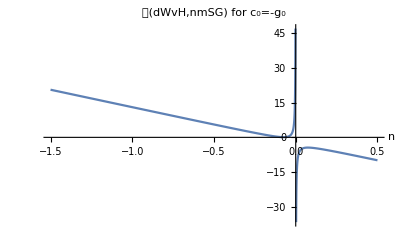

```mathematica
Plot[GadgetdWvHnmSGSetc0 ,{n,-1.5,0.5},AxesLabel->Automatic,PlotLabel->"𝒢(dWvH,nmSG) for c_0=-g_0"]
```

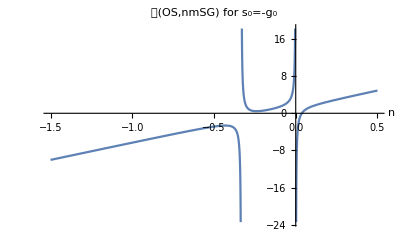

```mathematica
Plot[GadgetOSnmSGSets0,{n,-1.5,0.5},AxesLabel->Automatic,PlotLabel->"𝒢(OS,nmSG) for s_0=-g_0"]
```

#### Convergent cases for Gadget[dWvH,nmSG] exist for n = -1 and n = -1/3 and Gadget[OS,nmSG] for n = -1

#### dWvH,nmSG

Gadget[dWvH,nmSG], n = -1

```mathematica
Collect[Gadget[dWvH,nmSG]/.n-> -1/.c0-> c0plusg0 - g0,{c0plusg0},Simplify]/.c0plusg0-> c0+g0/.c0-> Subscript[c, 0]/.g0-> Subscript[g, 0]
```

13+38 (c_0+g_0)+40 (c_0+g_0)^2+18 (c_0+g_0)^3+3 (c_0+g_0)^4

```mathematica
TeXForm[%]
```

3 \left(c_0+g_0\right){}^4+18 \left(c_0+g_0\right){}^3+40 \left(c_0+g_0\right){}^2+38 \left(c_0+g_0\right)+13

```mathematica
Gadget[dWvH,nmSG]/.n-> -1/.c0-> -g0//Simplify
```

13

Gadget[dWvH,nmSG], n = -1/3

```mathematica
Collect[Gadget[dWvH,nmSG]/.n-> -1/3/.c0-> c0plusg0 - g0,{c0plusg0},Simplify]/.c0plusg0-> c0+g0/.c0-> Subscript[c, 0]/.g0-> Subscript[g, 0]
```

28/9+20/3 (c_0+g_0)+4 (c_0+g_0)^2

```mathematica
TeXForm[%]
```

4 \left(c_0+g_0\right){}^2+\frac{20}{3} \left(c_0+g_0\right)+\frac{28}{9}

```mathematica
Gadget[dWvH,nmSG]/.n-> -1/3/.c0-> -g0//Simplify
```

28/9

Gadget[OS,nmSG], n = -1

```mathematica
Collect[Gadget[OS,nmSG]/.n-> -1/.s0-> s0plusg0 - g0,{c0plusg0},Simplify]/.s0plusg0->s0+g0/.s0-> Subscript[s, 0]/.g0-> Subscript[g, 0]
```

-19/3-15 (g_0+s_0)-12 (g_0+s_0)^2-3 (g_0+s_0)^3

```mathematica
TeXForm[%]
```

-3 \left(g_0+s_0\right){}^3-12 \left(g_0+s_0\right){}^2-15 \left(g_0+s_0\right)-\frac{19}{3}

```mathematica
Gadget[OS,nmSG]/.n-> -1/.s0-> -g0//Simplify
```

-19/3